Preprosta vijačnica

```mathematica
ClearAll["Global`*"];
r[t_]:={5Cos[t],5Sin[t],t};
ParametricPlot3D[r[t],{t,-10,10},LabelStyle->Directive[Medium]]
```

-Graphics3D-

Lancretov izrek

```mathematica
ClearAll["Global`*"];
pts={{1,0,0},{0,1,0},{0,0,1},{Sqrt[2]/2,0,Sqrt[2]/2}};
Graphics3D[{Arrow[{{0,0,0},#}&/@pts],Dashed,Line[{{0,0,Sqrt[2]/2},{Sqrt[2]/2,0,Sqrt[2]/2},{Sqrt[2]/2,0,0}}],Text[Style[ToExpression["t",TeXForm,HoldForm],18],{0.95,0,-0.06}],Text[Style[ToExpression["p",TeXForm,HoldForm],18],{0,0.95,-0.06}],Text[Style[ToExpression["b",TeXForm,HoldForm],18],{0,0.07,0.95}],Text[Style[ToExpression["a",TeXForm,HoldForm],18],{Sqrt[2]/2+0.06,0,Sqrt[2]/2+0.06}],Text[Style[ToExpression["\psi",TeXForm,HoldForm],18],{0.15,0,0.06}]},Boxed->False]
```

-Graphics3D-

DPH krivulja stopnje 3

```mathematica
ClearAll["Global`*"];
<<Quaternions`
```

```mathematica
parameters = {α0 ,α1,β0,β1 };
Evaluate@parameters= {1,-ⅈ,1+ⅈ,1};
```

```mathematica
alphaList={α0,α1};
betaList={β0,β1};
```

```mathematica
quaternionCoeffs = (ToQuaternion[#]&/@alphaList) + (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList)
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

{Quaternion[1,0,1,1],Quaternion[0,-1,0,1]}

```mathematica
p0={0,0,0};
p1=p0+1/3 AA[0,0];
p2=p1+1/6(AA[0,1]+AA[1,0]);
p3=p2+1/3 AA[1,1];
```

```mathematica
points = {p0,p1,p2,p3};
N[points]
```

{{0.,0.,0.},{-0.333333,0.666667,-0.666667},{-0.666667,0.666667,-1.},{-0.666667,0.666667,-1.66667}}

```mathematica
Graphics3D[{Thick,BezierCurve[points, SplineDegree->3],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

-Graphics3D-

```mathematica
r[t_]=∑_(i=0)^3 points⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[r[t]]
ExpandAll[r[t]]//TeXForm
```

{-t+t^3/3,2 t-2 t^2+(2 t^3)/3,-2 t+t^2-(2 t^3)/3}

\left\{\frac{t^3}{3}-t,\frac{2 t^3}{3}-2 t^2+2 t,-\frac{2 t^3}{3}+t^2-2 t\right\}

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

(3-4 t+3 t^2)^2

```mathematica
σ[t_]:=3-4 t+3 t^2;
```

```mathematica
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

4

```mathematica
ω[t_]=2;
```

```mathematica
Simplify[Cross[dr[t],d2r[t]]]
```

{4 (-1+t^2),2 (1-4 t+t^2),4 (-1+t)^2}

```mathematica
Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]]
```

4 (3-4 t+3 t^2)^2

```mathematica
Simplify[Cross[dr[t],d2r[t]].d3r[t]]
```

-16

```mathematica
curvaturesRatio=Abs[ω[t]^3/Simplify[Cross[dr[t],d2r[t]].d3r[t]]]
```

1/2

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1

DPH krivulja stopnje 5

```mathematica
ClearAll["Global`*"];
<<Quaternions`
```

```mathematica
parameters ={a0, a1, b0, b1,w0,w1};
Evaluate@parameters= {1,ⅈ,1+ⅈ,2ⅈ,-1,-ⅈ};
```

```mathematica
alphaList={a0*w0,(1/2)(a0*w1+a1*w0),a1*w1};
betaList={b0*w0,(1/2)(b0*w1+b1*w0),b1*w1};
```

```mathematica
quaternionCoeffs = (ToQuaternion[#]&/@alphaList) + (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList)
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

{Quaternion[-1,0,-1,-1],Quaternion[0,-1,-3/2,1/2],Quaternion[1,0,0,2]}

```mathematica
p0={0,0,0};
p1=p0+1/5 AA[0,0];
p2=p1+1/10(AA[0,1]+AA[1,0]);
p3=p2+1/30(AA[0,2]+4AA[1,1]+AA[2,0]);
p4=p3+1/10(AA[1,2]+AA[2,1]);
p5=p4+1/5 AA[2,2];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5};
N[points]
```

{{0.,0.,0.},{-0.2,0.4,-0.4},{-0.4,0.5,-0.5},{-0.533333,0.7,-0.566667},{-0.733333,0.8,-0.666667},{-1.33333,1.6,-0.666667}}

```mathematica
Graphics3D[{Thick,BezierCurve[points, SplineDegree->5],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

-Graphics3D-

```mathematica
r[t_]=∑_(i=0)^5 points⟦i+1⟧Binomial[5,i](1-t)^(5-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[r[t]]
ExpandAll[r[t]]//TeXForm
```

{-t+(2 t^3)/3-t^4,2 t-3 t^2+4 t^3-3 t^4+(8 t^5)/5,-2 t+3 t^2-(8 t^3)/3+t^4}

\left\{-t^4+\frac{2 t^3}{3}-t,\frac{8 t^5}{5}-3 t^4+4 t^3-3 t^2+2 t,t^4-\frac{8 t^3}{3}+3 t^2-2 t\right\}

```mathematica
ExpandAll[dr[t]]//TeXForm
```

\left\{-4 t^3+2 t^2-1,8 t^4-12 t^3+12 t^2-6 t+2,4 t^3-8 t^2+6 t-2\right\}

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

(3-8 t+14 t^2-12 t^3+8 t^4)^2

```mathematica
σ[t_]:=3-8 t+14 t^2-12 t^3+8 t^4//TeXForm
```

```mathematica
Simplify[Cross[dr[t],d2r[t]]]
```

{-8 (-2+t) t (1-2 t+2 t^2)^2,6 (1-2 t+2 t^2)^2,-2 (1-2 t+2 t^2)^2 (-3+4 t+4 t^2)}

```mathematica
Simplify[Cross[dr[t],d2r[t]]]//TeXForm
```

\left\{-8 (t-2) t \left(2 t^2-2 t+1\right)^2,6 \left(2 t^2-2 t+1\right)^2,-2 \left(2 t^2-2 t+1\right)^2 \left(4 t^2+4 t-3\right)\right\}

```mathematica
Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]]//TeXForm
```

8 \left(2 t^2-2 t+1\right)^4 \left(4 t^2-2 t+3\right)^2

```mathematica
Simplify[Cross[dr[t],d2r[t]].d3r[t]]//TeXForm
```

48 \left(2 t^2-2 t+1\right)^3

```mathematica
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

8 (1-2 t+2 t^2)^2

```mathematica
ω[t_]=√8(1-2 t+2 t^2);
```

```mathematica
curvaturesRatio=Abs[ω[t]^3/Simplify[Cross[dr[t],d2r[t]].d3r[t]]]
```

(√2)/3

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1-2 t+2 t^2

PH krivulja stopnje 5

```mathematica
ClearAll["Global`*"];
<<Quaternions`
```

```mathematica
quaternionCoeffs = {Quaternion[1,0,1,0],Quaternion[1,2,1,-1],Quaternion[0,-1,1,1]};
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

```mathematica
p0={0,0,0};
p1=p0+1/5 AA[0,0];
p2=p1+1/10(AA[0,1]+AA[1,0]);
p3=p2+1/30(AA[0,2]+4AA[1,1]+AA[2,0]);
p4=p3+1/10(AA[1,2]+AA[2,1]);
p5=p4+1/5 AA[2,2];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5}
```

{{0,0,0},{0,0,-2/5},{0,1/5,-4/5},{1/3,7/15,-5/3},{-1/15,13/15,-19/15},{-4/15,7/15,-5/3}}

```mathematica
Graphics3D[{Thick,BezierCurve[points, SplineDegree->5],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

-Graphics3D-

```mathematica
r[t_]=∑_(i=0)^5 points⟦i+1⟧Binomial[5,i](1-t)^(5-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[r[t]]
ExpandAll[r[t]]//TeXForm
```

{(10 t^3)/3-7 t^4+(17 t^5)/5,2 t^2-(4 t^3)/3+t^4-(6 t^5)/5,-2 t-(14 t^3)/3+11 t^4-6 t^5}

\left\{\frac{17 t^5}{5}-7 t^4+\frac{10 t^3}{3},-\frac{6 t^5}{5}+t^4-\frac{4 t^3}{3}+2 t^2,-6 t^5+11 t^4-\frac{14 t^3}{3}-2 t\right\}

```mathematica
ExpandAll[dr[t]]//TeXForm
```

\left\{-4 t^3+2 t^2-1,8 t^4-12 t^3+12 t^2-6 t+2,4 t^3-8 t^2+6 t-2\right\}

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

(2+18 t^2-52 t^3+35 t^4)^2

```mathematica
σ[t_]:=2+18 t^2-52 t^3+35 t^4//TeXForm
```

```mathematica
Simplify[σ[t]]
```

35 t^4-52 t^3+18 t^2+2

```mathematica
Simplify[Cross[dr[t],d2r[t]]]
```

{8 (1-2 t-4 t^2+38 t^3-60 t^4+9 t^5+18 t^6),-4 t (10-42 t+34 t^2+12 t^3-31 t^4+23 t^5),4 t^2 (-10+56 t-69 t^2+4 t^3+25 t^4)}

```mathematica
Simplify[Cross[dr[t],d2r[t]]]//TeXForm
```

\left\{-8 (t-2) t \left(2 t^2-2 t+1\right)^2,6 \left(2 t^2-2 t+1\right)^2,-2 \left(2 t^2-2 t+1\right)^2 \left(4 t^2+4 t-3\right)\right\}

```mathematica
Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]]//TeXForm
```

16 \left(2 t^4+6 t^3+3 t^2-4 t+1\right) \left(35 t^4-52 t^3+18 t^2+2\right)^2

```mathematica
Simplify[Cross[dr[t],d2r[t]].d3r[t]]
```

16 (10-84 t+156 t^2-40 t^3-57 t^4-138 t^5+51 t^6)

```mathematica
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

16 (1-4 t+3 t^2+6 t^3+2 t^4)

```mathematica
ω[t_]=Simplify[Sqrt[-4 t+3 t^2+6 t^3+2 t^4]];
```

```mathematica
curvaturesRatio=Abs[ω[t]^3/Simplify[Cross[dr[t],d2r[t]].d3r[t]]]
```

1/16 Abs[((t (-4+3 t+6 t^2+2 t^3))^(3/2))/(10-84 t+156 t^2-40 t^3-57 t^4-138 t^5+51 t^6)]

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1

## Vijačna DPH krivulja stopnje 7

```mathematica
<<Quaternions`
```

## Vijačne DPH krivulje stopnje 7

### Primer 1: (Kubična reparametrizacija)

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

Uporabimo kompleksno premico/krožnico, definirano z:

```mathematica
parameters ={a0, a1, b0, b1};
Evaluate@parameters = {1,1+ⅈ,1-ⅈ,ⅈ};
```

```mathematica
z[t_]= (a0 (1-t)+a1 t)/(b0(1-t)+b1 t);
```

Reparametrizacijska funkcija z2:

```mathematica
fBernPolyCoeff={1,2,2,1};
gBernPolyCoeff={1,2,3,3};
```

```mathematica
fBernPoly[x_]=Sum[k, {k, fBernPolyCoeff⟦#+1⟧BernsteinBasis[3,#,x]&/@Range[0,3]}];
gBernPoly[x_]=Sum[k, {k, gBernPolyCoeff⟦#+1⟧BernsteinBasis[3,#,x]&/@Range[0,3]}];
z2[t_]=fBernPoly[t]/gBernPoly[t];
```

```mathematica
alphaList = fBernPolyCoeff⟦#+1⟧(a1-a0)+gBernPolyCoeff⟦#+1⟧a0&/@Range[0,3];
betaList = fBernPolyCoeff⟦#+1⟧(b1-b0)+gBernPolyCoeff⟦#+1⟧b0&/@Range[0,3];
```

```mathematica
quaternionCoeffs = (ToQuaternion[#]&/@alphaList) + (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList);
```

```mathematica
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

```mathematica
p0={0,0,0};
p1=p0+1/7 AA[0,0];
p2=p1+1/14(AA[0,1]+AA[1,0]);
p3=p2+1/35(AA[0,2]+3AA[1,1]+AA[2,0]);
p4=p3+1/140(AA[0,3]+9AA[1,2]+9AA[2,1]+AA[3,0]);
p5=p4+1/35(AA[1,3]+3AA[2,2]+AA[3,1]);
p6=p5+1/14(AA[2,3]+AA[3,2]);
p7=p6+1/7 AA[3,3];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5,p6,p7}
N[points]
Graphics3D[{Thick,BezierCurve[points, SplineDegree->7],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

{{0,0,0},{1/7,2/7,-2/7},{3/7,6/7,-6/7},{1,62/35,-12/7},{21/10,99/35,-87/35},{253/70,137/35,-93/35},{353/70,177/35,-68/35},{403/70,227/35,-18/35}}

{{0.,0.,0.},{0.142857,0.285714,-0.285714},{0.428571,0.857143,-0.857143},{1.,1.77143,-1.71429},{2.1,2.82857,-2.48571},{3.61429,3.91429,-2.65714},{5.04286,5.05714,-1.94286},{5.75714,6.48571,-0.514286}}

-Graphics3D-

```mathematica
points // TeXForm
```

\left(
\begin{array}{ccc}
 0 & 0 & 0 \\
 \frac{1}{7} & \frac{2}{7} & -\frac{2}{7} \\
 \frac{3}{7} & \frac{6}{7} & -\frac{6}{7} \\
 1 & \frac{62}{35} & -\frac{12}{7} \\
 \frac{21}{10} & \frac{99}{35} & -\frac{87}{35} \\
 \frac{253}{70} & \frac{137}{35} & -\frac{93}{35} \\
 \frac{353}{70} & \frac{177}{35} & -\frac{68}{35} \\
 \frac{403}{70} & \frac{227}{35} & -\frac{18}{35} \\
\end{array}
\right)

```mathematica
r[t_]=∑_(i=0)^7 points⟦i+1⟧Binomial[7,i](1-t)^(7-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
Simplify[r[t]]
Simplify[dr[t]]
```

{t+3 t^2+5 t^3+(7 t^4)/2-(48 t^5)/5+3 t^6-t^7/7,2 t+6 t^2+2 t^3-9 t^4+(36 t^5)/5-2 t^6+(2 t^7)/7,-2 t-6 t^2+13 t^4-(24 t^5)/5-t^6+(2 t^7)/7}

{1+6 t+15 t^2+14 t^3-48 t^4+18 t^5-t^6,2 (1+6 t+3 t^2-18 t^3+18 t^4-6 t^5+t^6),2 (-1-6 t+26 t^3-12 t^4-3 t^5+t^6)}

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

9 (1+6 t+3 t^2-18 t^3+18 t^4-6 t^5+t^6)^2

```mathematica
σ[t_]=3(1+6 t+3 t^2-18 t^3+18 t^4-6 t^5+t^6);
```

```mathematica
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

180 t^2 (2+2 t-2 t^2+t^3)^2

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1

```mathematica
ω[t_]=√180 t(2+2 t-2 t^2+t^3);
```

```mathematica
curvaturesRatio=Abs[ω[t]^3/Simplify[Cross[dr[t],d2r[t]].d3r[t]]]
```

(√5)/2

### Primer 2: (Kvadratična polinomska multiplikacija)

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

```mathematica
parameters ={a0, a1, b0, b1,w0,w1,w2};
Evaluate@parameters= {5ⅈ,1+ⅈ,1-ⅈ,2+5ⅈ,1,1+ⅈ,1};
```

```mathematica
alphaList={a0 w0, 1/3(2a0 w1+a1 w0),1/3(2a1 w1+a0 w2), a1 w2};
betaList={b0 w0, 1/3(2b0 w1+b1 w0),1/3(2b1 w1+b0 w2), b1 w2};
```

```mathematica
quaternionCoeffs = (ToQuaternion[#]&/@alphaList) + (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList);
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

```mathematica
p0={0,0,0};
p1=p0+1/7 AA[0,0];
p2=p1+1/14(AA[0,1]+AA[1,0]);
p3=p2+1/35(AA[0,2]+3AA[1,1]+AA[2,0]);
p4=p3+1/140(AA[0,3]+9AA[1,2]+9AA[2,1]+AA[3,0]);
p5=p4+1/35(AA[1,3]+3AA[2,2]+AA[3,1]);
p6=p5+1/14(AA[2,3]+AA[3,2]);
p7=p6+1/7 AA[3,3];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5,p6,p7}
N[points]
Graphics3D[{Thick,BezierCurve[points, SplineDegree->7],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

{{0,0,0},{23/7,-10/7,10/7},{41/7,-25/21,62/21},{42/5,-11/105,100/21},{66/7,376/105,692/105},{269/35,706/105,246/35},{577/105,971/105,246/35},{172/105,1181/105,216/35}}

{{0.,0.,0.},{3.28571,-1.42857,1.42857},{5.85714,-1.19048,2.95238},{8.4,-0.104762,4.7619},{9.42857,3.58095,6.59048},{7.68571,6.72381,7.02857},{5.49524,9.24762,7.02857},{1.6381,11.2476,6.17143}}

-Graphics3D-

```mathematica
points//TeXForm
```

\left(
\begin{array}{ccc}
 0 & 0 & 0 \\
 \frac{23}{7} & -\frac{10}{7} & \frac{10}{7} \\
 \frac{41}{7} & -\frac{25}{21} & \frac{62}{21} \\
 \frac{42}{5} & -\frac{11}{105} & \frac{100}{21} \\
 \frac{66}{7} & \frac{376}{105} & \frac{692}{105} \\
 \frac{269}{35} & \frac{706}{105} & \frac{246}{35} \\
 \frac{577}{105} & \frac{971}{105} & \frac{246}{35} \\
 \frac{172}{105} & \frac{1181}{105} & \frac{216}{35} \\
\end{array}
\right)

```mathematica
r[t_]=∑_(i=0)^7 points⟦i+1⟧Binomial[7,i](1-t)^(7-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
Simplify[r[t]]
Simplify[dr[t]]
```

{23 t-15 t^2+24 t^3-76 t^4+(252 t^5)/5+(20 t^6)/3-(80 t^7)/7,-10 t+35 t^2-(86 t^3)/3+90 t^4-(784 t^5)/5+108 t^6-(184 t^7)/7,10 t+2 t^2+(20 t^3)/3-16 t^4-(72 t^5)/5+(88 t^6)/3-(80 t^7)/7}

{23-30 t+72 t^2-304 t^3+252 t^4+40 t^5-80 t^6,-2 (5-35 t+43 t^2-180 t^3+392 t^4-324 t^5+92 t^6),10+4 t+20 t^2-64 t^3-72 t^4+176 t^5-80 t^6}

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

(27-50 t+162 t^2-416 t^3+724 t^4-632 t^5+216 t^6)^2

```mathematica
σ[t_]=27-50 t+162 t^2-416 t^3+724 t^4-632 t^5+216 t^6;
```

```mathematica
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

3316 (1+4 t^2-8 t^3+4 t^4)^2

```mathematica
ω[t_]=√3316(1+4 t^2-8 t^3+4 t^4);
```

```mathematica
curvaturesRatio=Abs[ω[t]^3/Simplify[Cross[dr[t],d2r[t]].d3r[t]]]
```

(√829)/2

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1+4 t^2-8 t^3+4 t^4

```mathematica
tangentUnit[t_]=Simplify[dr[t]/σ[t]]
```

{(23-30 t-20 t^2)/(27-50 t+54 t^2),-(2 (5-35 t+23 t^2))/(27-50 t+54 t^2),(10+4 t-20 t^2)/(27-50 t+54 t^2)}

```mathematica
NormOfCrossProductOfFirstTwoDerivatives[t_]=Simplify[σ[t]ω[t]]
```

2 √829 (1+4 t^2-8 t^3+4 t^4) (27-50 t+162 t^2-416 t^3+724 t^4-632 t^5+216 t^6)

```mathematica
normalUnit[t]=Simplify[Cross[Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]],tangentUnit[t]]]
```

{(2 (85-891 t+655 t^2))/(√829 (27-50 t+54 t^2)),(695-702 t-740 t^2)/(√829 (27-50 t+54 t^2)),(8 (38-135 t+49 t^2))/(√829 (27-50 t+54 t^2))}

```mathematica
binormalUnit[t]=Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]]
```

{(-370+660 t-608 t^2)/(√829 (27-50 t+54 t^2)),-(4 (49-65 t+85 t^2))/(√829 (27-50 t+54 t^2)),(655-1258 t+1390 t^2)/(√829 (27-50 t+54 t^2))}

### Primer 3: (Reparametrizacija in multiplikacija)

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

```mathematica
parameters = {a0,a1,b0,b1,f0,f1,f2,g0,g1,g2,w0,w1};
Evaluate@parameters= {1+ⅈ,1,1-ⅈ,2,1,2,1,1,2,2,1,1+ⅈ};
```

```mathematica
Subscript[α, 0]=(f0(a1-a0)+g0 a0)w0;
Subscript[α, 1]=1/3((f0(a1-a0)+g0 a0)w1 +2(f1(a1-a0)+g1 a0)w0);
Subscript[α, 2]=1/3((f2(a1-a0)+g2 a0)w0+2(f1(a1-a0)+g1 a0)w1);
Subscript[α, 3]=(f2(a1-a0)+g2 a0)w1;
Subscript[β, 0]=(f0(b1-b0)+g0 b0)w0;
Subscript[β, 1]=1/3((f0(b1-b0)+g0 b0)w1 +2(f1(b1-b0)+g1 b0)w0);
Subscript[β, 2]=1/3((f2(b1-b0)+g2 b0)w0+2(f1(b1-b0)+g1 b0)w1);
Subscript[β, 3]=(f2(b1-b0)+g2 b0)w1;
alphaList={Subscript[α, 0],Subscript[α, 1],Subscript[α, 2],Subscript[α, 3]};
betaList={Subscript[β, 0],Subscript[β, 1],Subscript[β, 2],Subscript[β, 3]};
```

```mathematica
quaternionCoeffs = (ToQuaternion[#]&/@alphaList) + (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList);
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

```mathematica
p0={0,0,0};
p1=p0+1/7 AA[0,0];
p2=p1+1/14(AA[0,1]+AA[1,0]);
p3=p2+1/35(AA[0,2]+3AA[1,1]+AA[2,0]);
p4=p3+1/140(AA[0,3]+9AA[1,2]+9AA[2,1]+AA[3,0]);
p5=p4+1/35(AA[1,3]+3AA[2,2]+AA[3,1]);
p6=p5+1/14(AA[2,3]+AA[3,2]);
p7=p6+1/7 AA[3,3];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5,p6,p7}
N[points]
Graphics3D[{Thick,BezierCurve[points, SplineDegree->7],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

{{0,0,0},{-3/7,4/7,0},{-8/7,32/21,0},{-46/21,62/21,2/35},{-374/105,517/105,11/35},{-37/7,53/7,103/105},{-148/21,75/7,13/5},{-178/21,95/7,191/35}}

{{0.,0.,0.},{-0.428571,0.571429,0.},{-1.14286,1.52381,0.},{-2.19048,2.95238,0.0571429},{-3.5619,4.92381,0.314286},{-5.28571,7.57143,0.980952},{-7.04762,10.7143,2.6},{-8.47619,13.5714,5.45714}}

-Graphics3D-

```mathematica
points//TeXForm
```

\left(
\begin{array}{ccc}
 0 & 0 & 0 \\
 -\frac{3}{7} & \frac{4}{7} & 0 \\
 -\frac{8}{7} & \frac{32}{21} & 0 \\
 -\frac{46}{21} & \frac{62}{21} & \frac{2}{35} \\
 -\frac{374}{105} & \frac{517}{105} & \frac{11}{35} \\
 -\frac{37}{7} & \frac{53}{7} & \frac{103}{105} \\
 -\frac{148}{21} & \frac{75}{7} & \frac{13}{5} \\
 -\frac{178}{21} & \frac{95}{7} & \frac{191}{35} \\
\end{array}
\right)

```mathematica
r[t_]=∑_(i=0)^7 points⟦i+1⟧Binomial[7,i](1-t)^(7-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
Simplify[r[t]]
Simplify[r[t]]//TeXForm
```

{-3 t-6 t^2-(5 t^3)/3+2 t^4-2 t^5+(10 t^6)/3-(8 t^7)/7,4 t+8 t^2+(10 t^3)/3-t^4+2 t^5-(10 t^6)/3+(4 t^7)/7,2 t^3+3 t^4-(2 t^5)/5+2 t^6-(8 t^7)/7}

\left\{-\frac{8 t^7}{7}+\frac{10 t^6}{3}-2 t^5+2 t^4-\frac{5 t^3}{3}-6 t^2-3 t,\frac{4 t^7}{7}-\frac{10 t^6}{3}+2 t^5-t^4+\frac{10 t^3}{3}+8 t^2+4 t,-\frac{8 t^7}{7}+2 t^6-\frac{2 t^5}{5}+3 t^4+2 t^3\right\}

```mathematica
Simplify[dr[t]]
Simplify[dr[t]]//TeXForm
```

{-3-12 t-5 t^2+8 t^3-10 t^4+20 t^5-8 t^6,2 (2+8 t+5 t^2-2 t^3+5 t^4-10 t^5+2 t^6),-2 t^2 (-3-6 t+t^2-6 t^3+4 t^4)}

\left\{-8 t^6+20 t^5-10 t^4+8 t^3-5 t^2-12 t-3,2 \left(2 t^6-10 t^5+5 t^4-2 t^3+5 t^2+8 t+2\right),-2 t^2 \left(4 t^4-6 t^3+t^2-6 t-3\right)\right\}

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

(5+20 t+11 t^2-8 t^3+18 t^4-28 t^5+12 t^6)^2

```mathematica
σ[t_]=5+20 t+11 t^2-8 t^3+18 t^4-28 t^5+12 t^6;
σ[t]//TeXForm
```

12 t^6-28 t^5+18 t^4-8 t^3+11 t^2+20 t+5

```mathematica
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

160 t^2 (1+t+t^2+t^3)^2

```mathematica
ω[t_]=√160 t(1+t+t^2+t^3);
```

```mathematica
curvaturesRatio=Abs[ω[t]^3/Simplify[Cross[dr[t],d2r[t]].d3r[t]]]
```

√10

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1+t^2

```mathematica
tangentUnit[t_]=Simplify[dr[t]/σ[t]]
```

{-(3+12 t+2 t^2-20 t^3+8 t^4)/(5+20 t+6 t^2-28 t^3+12 t^4),(4+16 t+6 t^2-20 t^3+4 t^4)/(5+20 t+6 t^2-28 t^3+12 t^4),(2 t^2 (3+6 t-4 t^2))/(5+20 t+6 t^2-28 t^3+12 t^4)}

```mathematica
NormOfCrossProductOfFirstTwoDerivatives[t_]=Simplify[σ[t]ω[t]]
```

4 √10 t (1+t+t^2+t^3) (5+20 t+11 t^2-8 t^3+18 t^4-28 t^5+12 t^6)

```mathematica
normalUnit[t]=Simplify[Cross[Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]],tangentUnit[t]]]
```

{-(2 √(2/5) (-1-4 t-3 t^2+2 t^3+t^4))/(5+20 t+6 t^2-28 t^3+12 t^4),(3+12 t-16 t^2-56 t^3+32 t^4)/(√10 (5+20 t+6 t^2-28 t^3+12 t^4)),(√(5/2) (3+12 t+4 t^2-16 t^3+4 t^4))/(5+20 t+6 t^2-28 t^3+12 t^4)}

```mathematica
binormalUnit[t]=Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]]
```

{(2 √(2/5) (3+12 t+4 t^2-16 t^3+7 t^4))/(5+20 t+6 t^2-28 t^3+12 t^4),((3+6 t-4 t^2)^2)/(√10 (5+20 t+6 t^2-28 t^3+12 t^4)),-(√(5/2) (1+2 t-2 t^2)^2)/(5+20 t+6 t^2-28 t^3+12 t^4)}

## DPH krivulje z deg(h)=0, deg(w)=2

### Primer 4: (deg(h)=0, deg(w)=2, vijačna)

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

```mathematica
parameters = {h0,w0,w1,w2,α0 ,α1,β0 };
Evaluate@parameters= {1,1,1+ⅈ,ⅈ,1,2ⅈ,ⅈ};
```

```mathematica
solutions=Solve[3(α0 β1-α1 β0)==w0^2 && 3(α0 β2-α2 β0)==2w0 w1 && (α0 β3-α3 β0)+3(α1 β2-α2 β1)==2/3(2 w1^2+w0 w2)&& 3(α1 β3-α3 β1)==2w1 w2 && 3(α2 β3-α3 β2)==w2^2&& (α1 β2-α2 β1)==1/9(4w1^2- w0 w2)&&(α0 β1-α1 β0)(α2 β3-α3 β2)==(α0 β2-α2 β0)(α1 β3-α3 β1)-(α1 β2-α2 β1)(α0 β3-α3 β0),{α2,α3,β1,β2,β3}]
```

{{α2→-4+(5 ⅈ)/3,α3→-4-2 ⅈ,β1→-5/3,β2→-1-(10 ⅈ)/3,β3→2-3 ⅈ}}

```mathematica
alphaList={α0,α1,α2/.solutions⟦1⟧,α3/.solutions⟦1⟧};
betaList={β0,β1/.solutions⟦1⟧,β2/.solutions⟦1⟧,β3/.solutions⟦1⟧};
```

```mathematica
quaternionCoeffs = (ToQuaternion[#]&/@alphaList) + (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList)
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

{Quaternion[1,0,1,0],Quaternion[0,2,0,-5/3],Quaternion[-4,5/3,-10/3,-1],Quaternion[-4,-2,-3,2]}

```mathematica
p0={0,0,0};
p1=p0+1/7 AA[0,0];
p2=p1+1/14(AA[0,1]+AA[1,0]);
p3=p2+1/35(AA[0,2]+3AA[1,1]+AA[2,0]);
p4=p3+1/140(AA[0,3]+9AA[1,2]+9AA[2,1]+AA[3,0]);
p5=p4+1/35(AA[1,3]+3AA[2,2]+AA[3,1]);
p6=p5+1/14(AA[2,3]+AA[3,2]);
p7=p6+1/7 AA[3,3];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5,p6,p7}
N[points]
Graphics3D[{Thick,BezierCurve[points, SplineDegree->7],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

{{0,0,0},{0,0,-2/7},{0,1/21,-2/7},{1/15,3/35,-46/105},{4/15,3/35,-20/21},{4/5,-1/7,-326/105},{22/15,-10/21,-626/105},{37/15,-22/21,-158/15}}

{{0.,0.,0.},{0.,0.,-0.285714},{0.,0.047619,-0.285714},{0.0666667,0.0857143,-0.438095},{0.266667,0.0857143,-0.952381},{0.8,-0.142857,-3.10476},{1.46667,-0.47619,-5.9619},{2.46667,-1.04762,-10.5333}}

-Graphics3D-

```mathematica
points//TeXForm
```

\left(
\begin{array}{ccc}
 0 & 0 & 0 \\
 0 & 0 & -\frac{2}{7} \\
 0 & \frac{1}{21} & -\frac{2}{7} \\
 \frac{1}{15} & \frac{3}{35} & -\frac{46}{105} \\
 \frac{4}{15} & \frac{3}{35} & -\frac{20}{21} \\
 \frac{4}{5} & -\frac{1}{7} & -\frac{326}{105} \\
 \frac{22}{15} & -\frac{10}{21} & -\frac{626}{105} \\
 \frac{37}{15} & -\frac{22}{21} & -\frac{158}{15} \\
\end{array}
\right)

```mathematica
r[t_]=∑_(i=0)^7 points⟦i+1⟧Binomial[7,i](1-t)^(7-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
Simplify[r[t]]
Simplify[r[t]]//TeXForm
```

{1/15 t^3 (35+42 t^2-70 t^3+30 t^4),t^2-2 t^3+t^4-4 t^5+(14 t^6)/3-(12 t^7)/7,-2 t+6 t^2-(46 t^3)/3+8 t^4-(136 t^5)/5+32 t^6-12 t^7}

\left\{\frac{1}{15} t^3 \left(30 t^4-70 t^3+42 t^2+35\right),-\frac{12 t^7}{7}+\frac{14 t^6}{3}-4 t^5+t^4-2 t^3+t^2,-12 t^7+32 t^6-\frac{136 t^5}{5}+8 t^4-\frac{46 t^3}{3}+6 t^2-2 t\right\}

```mathematica
Simplify[dr[t]]
Simplify[dr[t]]//TeXForm
```

{7 (t^2+2 t^4-4 t^5+2 t^6),2 t (1-3 t+2 t^2-10 t^3+14 t^4-6 t^5),-2 (1-6 t+23 t^2-16 t^3+68 t^4-96 t^5+42 t^6)}

\left\{7 \left(2 t^6-4 t^5+2 t^4+t^2\right),2 t \left(-6 t^5+14 t^4-10 t^3+2 t^2-3 t+1\right),-2 \left(42 t^6-96 t^5+68 t^4-16 t^3+23 t^2-6 t+1\right)\right\}

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1+2 t^2-4 t^3+2 t^4

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

(2-12 t+47 t^2-32 t^3+138 t^4-196 t^5+86 t^6)^2

```mathematica
σ[t_]=2-12 t+47 t^2-32 t^3+138 t^4-196 t^5+86 t^6;
```

```mathematica
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

4 (1+2 t^2-4 t^3+2 t^4)^2

```mathematica
ω[t_]=2(1+2 t^2-4 t^3+2 t^4);
```

```mathematica
curvaturesRatio=Abs[ω[t]^3/Simplify[Cross[dr[t],d2r[t]].d3r[t]]]
```

1/7

```mathematica
tangentUnit[t_]=Simplify[dr[t]/σ[t]]
```

{(7 t^2)/(2-12 t+43 t^2),(2 (1-3 t) t)/(2-12 t+43 t^2),-(2 (1-6 t+21 t^2))/(2-12 t+43 t^2)}

```mathematica
NormOfCrossProductOfFirstTwoDerivatives[t_]=Simplify[σ[t]ω[t]]
```

2 (1+2 t^2-4 t^3+2 t^4) (2-12 t+47 t^2-32 t^3+138 t^4-196 t^5+86 t^6)

```mathematica
normalUnit[t]=Simplify[Cross[Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]],tangentUnit[t]]]
```

{(14 (1-3 t) t)/(2-12 t+43 t^2),(2-12 t-7 t^2)/(2-12 t+43 t^2),(2 (1-3 t) t)/(2-12 t+43 t^2)}

```mathematica
binormalUnit[t]=Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]]
```

{(2-12 t-6 t^2)/(2-12 t+43 t^2),(14 t (-1+3 t))/(2-12 t+43 t^2),-(7 t^2)/(2-12 t+43 t^2)}

### Primer 5: (deg(h)=0, deg(w)=2, ne-vijačna)

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

```mathematica
parameters = {h0,w0,w1,w2,α0 ,α1,β0 };
Evaluate@parameters= {1,1,1+ⅈ,ⅈ,1,2ⅈ,ⅈ};
```

```mathematica
solutions=Solve[3(α0 β1-α1 β0)==w0^2 && 3(α0 β2-α2 β0)==2w0 w1 && (α0 β3-α3 β0)+3(α1 β2-α2 β1)==2/3(2 w1^2+w0 w2)&& 3(α1 β3-α3 β1)==2w1 w2 && 3(α2 β3-α3 β2)==w2^2&& (α1 β2-α2 β1)==1/3(w0 w2)&&(α0 β1-α1 β0)(α2 β3-α3 β2)==(α0 β2-α2 β0)(α1 β3-α3 β1)-(α1 β2-α2 β1)(α0 β3-α3 β0),{α2,α3,β1,β2,β3}]
```

{{α2→-4+3 ⅈ,α3→-12-2 ⅈ,β1→-5/3,β2→-7/3-(10 ⅈ)/3,β3→2-(29 ⅈ)/3}}

```mathematica
alphaList={α0,α1,α2/.solutions⟦1⟧,α3/.solutions⟦1⟧};
betaList={β0,β1/.solutions⟦1⟧,β2/.solutions⟦1⟧,β3/.solutions⟦1⟧};
α[t_]=∑_(i=0)^3 alphaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
β[t_]=∑_(i=0)^3 betaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
```

```mathematica
quaternionCoeffs = (ToQuaternion[#]&/@alphaList) + (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList)
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

{Quaternion[1,0,1,0],Quaternion[0,2,0,-5/3],Quaternion[-4,3,-10/3,-7/3],Quaternion[-12,-2,-29/3,2]}

```mathematica
p0={0,0,0};
p1=p0+1/7 AA[0,0];
p2=p1+1/14(AA[0,1]+AA[1,0]);
p3=p2+1/35(AA[0,2]+3AA[1,1]+AA[2,0]);
p4=p3+1/140(AA[0,3]+9AA[1,2]+9AA[2,1]+AA[3,0]);
p5=p4+1/35(AA[1,3]+3AA[2,2]+AA[3,1]);
p6=p5+1/14(AA[2,3]+AA[3,2]);
p7=p6+1/7 AA[3,3];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5,p6,p7}
N[points]
Graphics3D[{Thick,BezierCurve[points, SplineDegree->7],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

{{0,0,0},{0,0,-2/7},{0,1/21,-2/7},{1/15,3/35,-46/105},{32/105,3/35,-48/35},{104/105,1/105,-466/105},{962/315,-34/105,-1486/105},{1079/105,-58/35,-5086/105}}

{{0.,0.,0.},{0.,0.,-0.285714},{0.,0.047619,-0.285714},{0.0666667,0.0857143,-0.438095},{0.304762,0.0857143,-1.37143},{0.990476,0.00952381,-4.4381},{3.05397,-0.32381,-14.1524},{10.2762,-1.65714,-48.4381}}

-Graphics3D-

```mathematica
points//TeXForm
```

\left(
\begin{array}{ccc}
 0 & 0 & 0 \\
 0 & 0 & -\frac{2}{7} \\
 0 & \frac{1}{21} & -\frac{2}{7} \\
 \frac{1}{15} & \frac{3}{35} & -\frac{46}{105} \\
 \frac{32}{105} & \frac{3}{35} & -\frac{48}{35} \\
 \frac{104}{105} & \frac{1}{105} & -\frac{466}{105} \\
 \frac{962}{315} & -\frac{34}{105} & -\frac{1486}{105} \\
 \frac{1079}{105} & -\frac{58}{35} & -\frac{5086}{105} \\
\end{array}
\right)

```mathematica
r[t_]=∑_(i=0)^7 points⟦i+1⟧Binomial[7,i](1-t)^(7-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
Expand[r[t]]
Expand[r[t]]//TeXForm
```

{(7 t^3)/3+(4 t^4)/3+(14 t^5)/5+(22 t^6)/9+(86 t^7)/63,t^2-2 t^3+t^4-(4 t^5)/5-(2 t^6)/3-(4 t^7)/21,-2 t+6 t^2-(46 t^3)/3-(20 t^4)/3-(56 t^5)/5-(40 t^6)/3-(124 t^7)/21}

\left\{\frac{86 t^7}{63}+\frac{22 t^6}{9}+\frac{14 t^5}{5}+\frac{4 t^4}{3}+\frac{7 t^3}{3},-\frac{4 t^7}{21}-\frac{2 t^6}{3}-\frac{4 t^5}{5}+t^4-2 t^3+t^2,-\frac{124 t^7}{21}-\frac{40 t^6}{3}-\frac{56 t^5}{5}-\frac{20 t^4}{3}-\frac{46 t^3}{3}+6 t^2-2 t\right\}

```mathematica
Simplify[dr[t]]
Simplify[dr[t]]//TeXForm
```

{1/9 t^2 (63+48 t+126 t^2+132 t^3+86 t^4),-2/3 t (-3+9 t-6 t^2+6 t^3+6 t^4+2 t^5),-2/3 (3-18 t+69 t^2+40 t^3+84 t^4+120 t^5+62 t^6)}

\left\{\frac{1}{9} t^2 \left(86 t^4+132 t^3+126 t^2+48 t+63\right),-\frac{2}{3} t \left(2 t^5+6 t^4+6 t^3-6 t^2+9 t-3\right),-\frac{2}{3} \left(62 t^6+120 t^5+84 t^4+40 t^3+69 t^2-18 t+3\right)\right\}

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1/9

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

1/81 (18-108 t+423 t^2+240 t^3+522 t^4+732 t^5+382 t^6)^2

```mathematica
σ[t_]=1/9(18-108 t+423 t^2+240 t^3+522 t^4+732 t^5+382 t^6);
Expand[σ[t]]//TeXForm
```

\frac{382 t^6}{9}+\frac{244 t^5}{3}+58 t^4+\frac{80 t^3}{3}+47 t^2-12 t+2

```mathematica
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

4 (1+2 t^2-4 t^3+2 t^4)^2

```mathematica
ω[t_]=2(1+2 t^2-4 t^3+2 t^4);
```

```mathematica
curvaturesRatio=Abs[Simplify[ω[t]^3/(Cross[dr[t],d2r[t]].d3r[t])]]
```

9 Abs[((1+2 t^2-4 t^3+2 t^4)^2)/(63+144 t-180 t^2+624 t^3+1272 t^4-2688 t^5-296 t^6-1840 t^7+460 t^8)]

```mathematica
w[t_]=w0(1-t)^2+2w1(1-t)t+w2 t^2
```

(1-t)^2+(2+2 ⅈ) (1-t) t+ⅈ t^2

```mathematica
roots = Solve[(1-t)^2+(2+2 ⅈ) (1-t) t+ⅈ t^2==0,t];
taus ={FullSimplify[t/.roots⟦2⟧],FullSimplify[t/.roots⟦1⟧]}
```

{1/2 ((1+ⅈ)+√2),1/2 ((1+ⅈ)-√2)}

Kot lahko vidimo spodaj smo v primeru (a): α(τ_i)≠0 in β(τ_i)≠0 za i=1,2

```mathematica
FullSimplify/@{α[taus⟦1⟧],α[taus⟦2⟧],β[taus⟦1⟧],β[taus⟦2⟧]}
```

{(-2-8 ⅈ)-(1+5 ⅈ) √2,(-2-8 ⅈ)+(1+5 ⅈ) √2,-2/3 ⅈ ((2+10 ⅈ)+(1+6 ⅈ) √2),2/3 ((10-2 ⅈ)-(6-ⅈ) √2)}

```mathematica
Expand[α[t]]
```

1-(3-6 ⅈ) t-(9+3 ⅈ) t^2-(1+5 ⅈ) t^3

```mathematica
bernsteincoefficients[pol_]:=Module[{t,n,a},t=Variables[pol][[1]];
n=Exponent[pol,t];
Table[a[k],{k,0,n}]/. SolveAlways[Sum[a[k] Binomial[n,k] (taus⟦2⟧-t)^(n-k) (t-taus⟦1⟧)^k,{k,0,n}]==pol,t][[1]]];
```

```mathematica
alphaBernsteinCoeffs = FullSimplify/@bernsteincoefficients[α[t]];
betaBernsteinCoeffs = FullSimplify/@bernsteincoefficients[β[t]];
a1=alphaBernsteinCoeffs⟦4⟧;
a2=-alphaBernsteinCoeffs⟦1⟧;
b1=betaBernsteinCoeffs⟦4⟧;
b2=-betaBernsteinCoeffs⟦1⟧;
FullSimplify[a1 b2-a2 b1]
```

-(ⅈ √2)/3

Zgornji rezultat pove, da lahko res uporabimo trditev 1 iz drugega članka (enačba 41)

```mathematica
alphaBernsteinCoeffs
```

{((-2+2 ⅈ)-(2-ⅈ) √2)/((-1+ⅈ)+√2),0,0,((4+6 ⅈ)-(3+4 ⅈ) √2)/((-1+ⅈ)+√2)}

Preverimo, da vse štima:

```mathematica
FullSimplify[α[t]-(a1(t-taus⟦1⟧)^3+a2(t-taus⟦2⟧)^3)]
FullSimplify[a1-1/2(√2 - 1+(4√2 - 5)ⅈ)]
FullSimplify[a2-(-1/2(√2 + 1+(4√2 + 5)ⅈ))]
FullSimplify[β[t]-(b1(t-taus⟦1⟧)^3+b2(t-taus⟦2⟧)^3)]
FullSimplify[b1-1/3(6-5√2 +(√2 - 1)ⅈ)]
FullSimplify[b2-1/3(6+5√2 -(√2 + 1)ⅈ)]
```

0

0

0

«3 more identical outputs»

### Primer 6: (deg(h)=2, deg(w)=1, vijačna)

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

```mathematica
parameters = {h0,h1,h2,w0,w1,α0 ,α1,β0 };
Evaluate@parameters= {1,2,1,ⅈ,1,1,1,-1};
```

```mathematica
solutions=Solve[3(α0 β1-α1 β0)==h0 w0^2 && 3(α0 β2-α2 β0)==h1 w0^2+h0 w0 w1 && (α0 β3-α3 β0)+3(α1 β2-α2 β1)==1/3(h2 w0^2+4h1 w0 w1 + h0 w1^2)&& 3(α1 β3-α3 β1)==h2 w0 w1+h1 w1^2 && 3(α2 β3-α3 β2)==h2 w1^2&& (α1 β2-α2 β1)==1/9(h2 w0^2+h1 w0 w1 + h0 w1^2)&&(α0 β1-α1 β0)(α2 β3-α3 β2)==(α0 β2-α2 β0)(α1 β3-α3 β1)-(α1 β2-α2 β1)(α0 β3-α3 β0),{α2,α3,β1,β2,β3}]
```

{{α2→2-ⅈ/3,α3→2-5 ⅈ,β1→-4/3,β2→-8/3+(2 ⅈ)/3,β3→-2+7 ⅈ}}

```mathematica
alphaList={α0,α1,α2/.solutions⟦1⟧,α3/.solutions⟦1⟧};
betaList={β0,β1/.solutions⟦1⟧,β2/.solutions⟦1⟧,β3/.solutions⟦1⟧};
α[t_]=∑_(i=0)^3 alphaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
β[t_]=∑_(i=0)^3 betaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
```

```mathematica
quaternionCoeffs = (ToQuaternion[#]&/@alphaList) + (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList)
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

{Quaternion[1,0,0,-1],Quaternion[1,0,0,-4/3],Quaternion[2,-1/3,2/3,-8/3],Quaternion[2,-5,7,-2]}

```mathematica
p0={0,0,0};
p1=p0+1/7 AA[0,0];
p2=p1+1/14(AA[0,1]+AA[1,0]);
p3=p2+1/35(AA[0,2]+3AA[1,1]+AA[2,0]);
p4=p3+1/140(AA[0,3]+9AA[1,2]+9AA[2,1]+AA[3,0]);
p5=p4+1/35(AA[1,3]+3AA[2,2]+AA[3,1]);
p6=p5+1/14(AA[2,3]+AA[3,2]);
p7=p6+1/7 AA[3,3];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5,p6,p7}
N[points]
Graphics3D[{Thick,BezierCurve[points, SplineDegree->7],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

{{0,0,0},{0,-2/7,0},{-1/21,-13/21,0},{-16/105,-39/35,-2/105},{-37/105,-13/7,-8/105},{-24/35,-323/105,-6/35},{-137/105,-548/105,-38/105},{-71/15,-1718/105,-158/105}}

{{0.,0.,0.},{0.,-0.285714,0.},{-0.047619,-0.619048,0.},{-0.152381,-1.11429,-0.0190476},{-0.352381,-1.85714,-0.0761905},{-0.685714,-3.07619,-0.171429},{-1.30476,-5.21905,-0.361905},{-4.73333,-16.3619,-1.50476}}

-Graphics3D-

```mathematica
points//TeXForm
```

\left(
\begin{array}{ccc}
 0 & 0 & 0 \\
 0 & -\frac{2}{7} & 0 \\
 -\frac{1}{21} & -\frac{13}{21} & 0 \\
 -\frac{16}{105} & -\frac{39}{35} & -\frac{2}{105} \\
 -\frac{37}{105} & -\frac{13}{7} & -\frac{8}{105} \\
 -\frac{24}{35} & -\frac{323}{105} & -\frac{6}{35} \\
 -\frac{137}{105} & -\frac{548}{105} & -\frac{38}{105} \\
 -\frac{71}{15} & -\frac{1718}{105} & -\frac{158}{105} \\
\end{array}
\right)

```mathematica
r[t_]=∑_(i=0)^7 points⟦i+1⟧Binomial[7,i](1-t)^(7-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[Simplify[r[t]]]
ExpandAll[Simplify[r[t]]]//TeXForm
```

{-t^2-t^3/3-t^4+(3 t^5)/5-t^6-2 t^7,-2 t-t^2-4 t^3+t^4-(18 t^5)/5+(2 t^6)/3-(52 t^7)/7,-(2 t^3)/3+(2 t^5)/5-(2 t^6)/3-(4 t^7)/7}

\left\{-2 t^7-t^6+\frac{3 t^5}{5}-t^4-\frac{t^3}{3}-t^2,-\frac{52 t^7}{7}+\frac{2 t^6}{3}-\frac{18 t^5}{5}+t^4-4 t^3-t^2-2 t,-\frac{4 t^7}{7}-\frac{2 t^6}{3}+\frac{2 t^5}{5}-\frac{2 t^3}{3}\right\}

```mathematica
ExpandAll[Simplify[dr[t]]]
ExpandAll[Simplify[dr[t]]]//TeXForm
```

{-2 t-t^2-4 t^3+3 t^4-6 t^5-14 t^6,-2-2 t-12 t^2+4 t^3-18 t^4+4 t^5-52 t^6,-2 t^2+2 t^4-4 t^5-4 t^6}

\left\{-14 t^6-6 t^5+3 t^4-4 t^3-t^2-2 t,-52 t^6+4 t^5-18 t^4+4 t^3-12 t^2-2 t-2,-4 t^6-4 t^5+2 t^4-2 t^2\right\}

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1-2 t+2 t^2

```mathematica
gcdOfAlphaBeta=PolynomialGCD[α[t],β[t]]
```

-1+(1+ⅈ) t

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

(2+2 t+13 t^2-4 t^3+17 t^4-2 t^5+54 t^6)^2

```mathematica
σ[t_]=2+2 t+13 t^2-4 t^3+17 t^4-2 t^5+54 t^6;
σ[t]//TeXForm
```

54 t^6-2 t^5+17 t^4-4 t^3+13 t^2+2 t+2

```mathematica
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

4 (1-4 t^2+8 t^3-4 t^4)^2

```mathematica
ω[t_]=2(1-4 t^2+8 t^3-4 t^4);
curvaturesRatio=Abs[Simplify[ω[t]^3/(Cross[dr[t],d2r[t]].d3r[t])]]
```

1/2

```mathematica
NormOfCrossProductOfFirstTwoDerivatives[t_]=Simplify[σ[t]ω[t]]
```

2 (1-4 t^2+8 t^3-4 t^4) (2+2 t+13 t^2-4 t^3+17 t^4-2 t^5+54 t^6)

```mathematica
tangentUnit[t_]=Simplify[dr[t]/σ[t]]
```

{-(t (2+5 t+10 t^2+7 t^3))/(2+6 t+21 t^2+26 t^3+27 t^4),-(2+6 t+20 t^2+24 t^3+26 t^4)/(2+6 t+21 t^2+26 t^3+27 t^4),-(2 t^2 (1+t)^2)/(2+6 t+21 t^2+26 t^3+27 t^4)}

```mathematica
normalUnit[t]=Simplify[Cross[Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]],tangentUnit[t]]]
```

{-(2 (1+3 t+8 t^2+8 t^3+11 t^4))/(2+6 t+21 t^2+26 t^3+27 t^4),(t (2+5 t+10 t^2+7 t^3))/(2+6 t+21 t^2+26 t^3+27 t^4),-(2 t (2+5 t+10 t^2+7 t^3))/(2+6 t+21 t^2+26 t^3+27 t^4)}

```mathematica
binormalUnit[t]=Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]]
```

{(2 t (2+5 t+10 t^2+7 t^3))/(2+6 t+21 t^2+26 t^3+27 t^4),-(2 t^2 (1+t)^2)/(2+6 t+21 t^2+26 t^3+27 t^4),-(2+6 t+17 t^2+18 t^3+23 t^4)/(2+6 t+21 t^2+26 t^3+27 t^4)}

```mathematica
κ[t_]=Simplify[NormOfCrossProductOfFirstTwoDerivatives[t]/σ[t]^3]
```

(2+4 t-4 t^2)/((1-2 t+2 t^2) (2+6 t+21 t^2+26 t^3+27 t^4)^2)

### Primer 7: (deg(h)=2, deg(w)=1, ne-vijačna)

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

```mathematica
parameters = {h0,h1,h2,w0,w1,α0 ,α1,β0 };
Evaluate@parameters= {1,2,1,ⅈ,1,1,1,-1};
```

```mathematica
solutions=Solve[3(α0 β1-α1 β0)==h0 w0^2 && 3(α0 β2-α2 β0)==h1 w0^2+h0 w0 w1 && (α0 β3-α3 β0)+3(α1 β2-α2 β1)==1/3(h2 w0^2+4h1 w0 w1 + h0 w1^2)&& 3(α1 β3-α3 β1)==h2 w0 w1+h1 w1^2 && 3(α2 β3-α3 β2)==h2 w1^2&& (α1 β2-α2 β1)==1/3(h1 w0 w1)&&(α0 β1-α1 β0)(α2 β3-α3 β2)==(α0 β2-α2 β0)(α1 β3-α3 β1)-(α1 β2-α2 β1)(α0 β3-α3 β0),{α2,α3,β1,β2,β3}]
```

{{α2→2+ⅈ,α3→2-ⅈ,β1→-4/3,β2→-8/3-(2 ⅈ)/3,β3→-2+(5 ⅈ)/3}}

```mathematica
alphaList={α0,α1,α2/.solutions⟦1⟧,α3/.solutions⟦1⟧};
betaList={β0,β1/.solutions⟦1⟧,β2/.solutions⟦1⟧,β3/.solutions⟦1⟧};
α[t_]=∑_(i=0)^3 alphaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
β[t_]=∑_(i=0)^3 betaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
```

```mathematica
quaternionCoeffs = (ToQuaternion[#]&/@alphaList) + (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList)
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

{Quaternion[1,0,0,-1],Quaternion[1,0,0,-4/3],Quaternion[2,1,-2/3,-8/3],Quaternion[2,-1,5/3,-2]}

```mathematica
p0={0,0,0};
p1=p0+1/7 AA[0,0];
p2=p1+1/14(AA[0,1]+AA[1,0]);
p3=p2+1/35(AA[0,2]+3AA[1,1]+AA[2,0]);
p4=p3+1/140(AA[0,3]+9AA[1,2]+9AA[2,1]+AA[3,0]);
p5=p4+1/35(AA[1,3]+3AA[2,2]+AA[3,1]);
p6=p5+1/14(AA[2,3]+AA[3,2]);
p7=p6+1/7 AA[3,3];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5,p6,p7}
N[points]
Graphics3D[{Thick,BezierCurve[points, SplineDegree->7],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

{{0,0,0},{0,-2/7,0},{-1/21,-13/21,0},{-16/105,-39/35,-2/105},{-37/105,-13/7,-4/35},{-64/105,-331/105,-38/105},{-247/315,-436/105,-58/105},{-109/105,-202/35,-14/15}}

{{0.,0.,0.},{0.,-0.285714,0.},{-0.047619,-0.619048,0.},{-0.152381,-1.11429,-0.0190476},{-0.352381,-1.85714,-0.114286},{-0.609524,-3.15238,-0.361905},{-0.784127,-4.15238,-0.552381},{-1.0381,-5.77143,-0.933333}}

-Graphics3D-

```mathematica
points//TeXForm
```

\left(
\begin{array}{ccc}
 0 & 0 & 0 \\
 0 & -\frac{2}{7} & 0 \\
 -\frac{1}{21} & -\frac{13}{21} & 0 \\
 -\frac{16}{105} & -\frac{39}{35} & -\frac{2}{105} \\
 -\frac{37}{105} & -\frac{13}{7} & -\frac{4}{35} \\
 -\frac{64}{105} & -\frac{331}{105} & -\frac{38}{105} \\
 -\frac{247}{315} & -\frac{436}{105} & -\frac{58}{105} \\
 -\frac{109}{105} & -\frac{202}{35} & -\frac{14}{15} \\
\end{array}
\right)

```mathematica
r[t_]=∑_(i=0)^7 points⟦i+1⟧Binomial[7,i](1-t)^(7-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
Simplify[r[t]]
ExpandAll[r[t]]//TeXForm
```

{-t^2-t^3/3-t^4+(11 t^5)/5-(5 t^6)/9-(22 t^7)/63,-2 t-t^2-4 t^3+t^4-(26 t^5)/5+(34 t^6)/3-(124 t^7)/21,-2/15 t^3 (5+10 t-3 t^2-15 t^3+10 t^4)}

\left\{-\frac{22 t^7}{63}-\frac{5 t^6}{9}+\frac{11
   t^5}{5}-t^4-\frac{t^3}{3}-t^2,-\frac{124 t^7}{21}+\frac{34 t^6}{3}-\frac{26
   t^5}{5}+t^4-4 t^3-t^2-2 t,-\frac{4 t^7}{3}+2 t^6+\frac{2 t^5}{5}-\frac{4
   t^4}{3}-\frac{2 t^3}{3}\right\}

```mathematica
Simplify[dr[t]]
ExpandAll[dr[t]]//TeXForm
```

{-1/9 t (18+9 t+36 t^2-99 t^3+30 t^4+22 t^5),-2/3 (3+3 t+18 t^2-6 t^3+39 t^4-102 t^5+62 t^6),-2/3 t^2 (3+8 t-3 t^2-18 t^3+14 t^4)}

\left\{-\frac{22 t^6}{9}-\frac{10 t^5}{3}+11 t^4-4 t^3-t^2-2 t,-\frac{124 t^6}{3}+68
   t^5-26 t^4+4 t^3-12 t^2-2 t-2,-\frac{28 t^6}{3}+12 t^5+2 t^4-\frac{16 t^3}{3}-2
   t^2\right\}

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1/9

```mathematica
gcdOfAlphaBeta=PolynomialGCD[α[t],β[t]]
```

1/3

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

1/81 (18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6)^2

```mathematica
σ[t_]=1/9(18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6);
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

4 (1-4 t^2+8 t^3-4 t^4)^2

```mathematica
Expand[σ[t]]//TeXForm
```

\frac{382 t^6}{9}-\frac{206 t^5}{3}+25 t^4-4 t^3+13 t^2+2 t+2

```mathematica
ω[t]=2(1-4 t^2+8 t^3-4 t^4);
curvaturesRatio=Abs[Simplify[ω[t]^3/(Cross[dr[t],d2r[t]].d3r[t])]]
```

9/2 Abs[((-1-2 t+2 t^2) (1-2 t+2 t^2)^2)/(9+54 t-126 t^2+228 t^3-60 t^4-276 t^5+92 t^6)]

```mathematica
NormOfCrossProductOfFirstTwoDerivatives[t_]=Simplify[σ[t]ω[t]]
```

2/9 (1-4 t^2+8 t^3-4 t^4) (18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6)

```mathematica
tangentUnit[t_]=Simplify[dr[t]/σ[t]]
```

{-(t (18+9 t+36 t^2-99 t^3+30 t^4+22 t^5))/(18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6),-(6 (3+3 t+18 t^2-6 t^3+39 t^4-102 t^5+62 t^6))/(18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6),-(6 t^2 (3+8 t-3 t^2-18 t^3+14 t^4))/(18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6)}

```mathematica
normalUnit[t]=Simplify[Cross[Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]],tangentUnit[t]]]
```

{-(6 (3-3 t+12 t^2-72 t^3+73 t^4-88 t^5+232 t^6-280 t^7+116 t^8))/((1-2 t+2 t^2) (18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6)),(t (18-27 t+54 t^2-201 t^3+204 t^4+68 t^5-208 t^6+108 t^7))/((1-2 t+2 t^2) (18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6)),-(2 t (18+45 t-42 t^2+51 t^3-492 t^4+888 t^5-568 t^6+148 t^7))/((1-2 t+2 t^2) (18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6))}

```mathematica
binormalUnit[t]=Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]]
```

{(6 t (6+15 t-14 t^2+13 t^3-156 t^4+292 t^5-192 t^6+52 t^7))/((1-2 t+2 t^2) (18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6)),(2 t^2 (-9-30 t+75 t^2-84 t^3+120 t^4-152 t^5+68 t^6))/((1-2 t+2 t^2) (18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6)),(-18+18 t-81 t^2+450 t^3-447 t^4+516 t^5-1364 t^6+1648 t^7-684 t^8)/((1-2 t+2 t^2) (18+18 t+117 t^2-36 t^3+225 t^4-618 t^5+382 t^6))}

## DPH krivulje z deg(h)=4, deg(w)=0

### Primer 8 (deg(h)=4, deg(w)=0, vijačna)

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

```mathematica
parameters = {h0,h1,h2,h3,h4,w0 ,α0,α1,β0 };
Evaluate@parameters= {-1,2,3,4,-5,1,1,1-ⅈ,-1+ⅈ};
```

```mathematica
solutions=Solve[3(α0 β1-α1 β0)==h0 w0^2 && 3(α0 β2-α2 β0)==2h1 w0^2 && (α0 β3-α3 β0)+3(α1 β2-α2 β1)==2h2 w0^2&& 3(α1 β3-α3 β1)==2h3 w0^2 && 3(α2 β3-α3 β2)==h4 w0^2&& (α1 β2-α2 β1)==1/9(3h2+Sqrt[9 h2^2+3h0 h4-12h1 h3] w0^2)&&(α0 β1-α1 β0)(α2 β3-α3 β2)==(α0 β2-α2 β0)(α1 β3-α3 β1)-(α1 β2-α2 β1)(α0 β3-α3 β0),{α2,α3,β1,β2,β3}]
```

{{α2→-1+4 ⅈ,α3→-1+9 ⅈ,β1→-1/3+2 ⅈ,β2→-5/3-5 ⅈ,β3→-5-10 ⅈ}}

```mathematica
alphaList={α0,α1,α2/.solutions⟦1⟧,α3/.solutions⟦1⟧};
betaList={β0,β1/.solutions⟦1⟧,β2/.solutions⟦1⟧,β3/.solutions⟦1⟧};
α[t_]=∑_(i=0)^3 alphaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
β[t_]=∑_(i=0)^3 betaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
```

```mathematica
quaternionCoeffs = (ToQuaternion[#]&/@alphaList) + (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList)
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

{Quaternion[1,0,1,-1],Quaternion[1,-1,2,-1/3],Quaternion[-1,4,-5,-5/3],Quaternion[-1,9,-10,-5]}

```mathematica
p0={0,0,0};
p1=p0+1/7 AA[0,0];
p2=p1+1/14(AA[0,1]+AA[1,0]);
p3=p2+1/35(AA[0,2]+3AA[1,1]+AA[2,0]);
p4=p3+1/140(AA[0,3]+9AA[1,2]+9AA[2,1]+AA[3,0]);
p5=p4+1/35(AA[1,3]+3AA[2,2]+AA[3,1]);
p6=p5+1/14(AA[2,3]+AA[3,2]);
p7=p6+1/7 AA[3,3];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5,p6,p7}
N[points]
Graphics3D[{Thick,Green,Line[points],Black,BezierCurve[points, SplineDegree->7],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->True]
```

{{0,0,0},{-1/7,-2/7,-2/7},{-1/3,-13/21,-4/7},{-8/21,-29/35,-26/35},{26/105,26/35,8/35},{-1/5,-16/15,-34/35},{-341/105,-429/35,-284/35},{-986/105,-1279/35,-834/35}}

{{0.,0.,0.},{-0.142857,-0.285714,-0.285714},{-0.333333,-0.619048,-0.571429},{-0.380952,-0.828571,-0.742857},{0.247619,0.742857,0.228571},{-0.2,-1.06667,-0.971429},{-3.24762,-12.2571,-8.11429},{-9.39048,-36.5429,-23.8286}}

-Graphics3D-

```mathematica
points//TeXForm
```

\left(
\begin{array}{ccc}
 0 & 0 & 0 \\
 -\frac{1}{7} & -\frac{2}{7} & -\frac{2}{7} \\
 -\frac{1}{3} & -\frac{13}{21} & -\frac{4}{7} \\
 -\frac{8}{21} & -\frac{29}{35} & -\frac{26}{35} \\
 \frac{26}{105} & \frac{26}{35} & \frac{8}{35} \\
 -\frac{1}{5} & -\frac{16}{15} & -\frac{34}{35} \\
 -\frac{341}{105} & -\frac{429}{35} & -\frac{284}{35} \\
 -\frac{986}{105} & -\frac{1279}{35} & -\frac{834}{35} \\
\end{array}
\right)

```mathematica
r[t_]=∑_(i=0)^7 points⟦i+1⟧Binomial[7,i](1-t)^(7-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[Simplify[r[t]]]
```

{-t-t^2+(20 t^3)/3+12 t^4-(276 t^5)/5+36 t^6-(48 t^7)/7,-2 t-t^2+6 t^3+52 t^4-(872 t^5)/5+100 t^6-(120 t^7)/7,-2 t+4 t^3+32 t^4-(552 t^5)/5+64 t^6-(80 t^7)/7}

```mathematica
ExpandAll[Simplify[r[t]]]//TeXForm
```

\left\{-\frac{48 t^7}{7}+36 t^6-\frac{276 t^5}{5}+12 t^4+\frac{20 t^3}{3}-t^2-t,-\frac{120 t^7}{7}+100 t^6-\frac{872 t^5}{5}+52 t^4+6 t^3-t^2-2 t,-\frac{80 t^7}{7}+64 t^6-\frac{552 t^5}{5}+32 t^4+4 t^3-2 t\right\}

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

(3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6)^2

```mathematica
σ[t_]=3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6;
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

4 (1-12 t+12 t^2-8 t^3+12 t^4)^2

```mathematica
σ[t]//TeXForm
```

152 t^6-744 t^5+1068 t^4-248 t^3-26 t^2+2 t+3

```mathematica
ω[t_]=2(1-12 t+12 t^2-8 t^3+12 t^4);
curvaturesRatio=Abs[Simplify[ω[t]^3/(Cross[dr[t],d2r[t]].d3r[t])]]
```

1/8

```mathematica
NormOfCrossProductOfFirstTwoDerivatives[t_]=Simplify[σ[t]ω[t]]
```

2 (1-12 t+12 t^2-8 t^3+12 t^4) (3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6)

```mathematica
tangentUnit[t_]=Simplify[dr[t]/σ[t]]
```

{(-1-2 t+20 t^2+48 t^3-276 t^4+216 t^5-48 t^6)/(3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6),-(2 (1+t-9 t^2-104 t^3+436 t^4-300 t^5+60 t^6))/(3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6),-(2 (1-6 t^2-64 t^3+276 t^4-192 t^5+40 t^6))/(3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6)}

```mathematica
normalUnit[t]=Simplify[Cross[Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]],tangentUnit[t]]]
```

{(2 (-1+5 t-9 t^2-136 t^3+524 t^4-348 t^5+60 t^6))/(3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6),-(1+10 t-76 t^2+16 t^3+276 t^4-312 t^5+80 t^6)/(3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6),(2+8 t-84 t^2+128 t^3-88 t^4-96 t^5+48 t^6)/(3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6)}

```mathematica
binormalUnit[t]=Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]]
```

{-(2 (1+6 t-54 t^2+56 t^3+36 t^4-120 t^5+40 t^6))/(3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6),-(2 (-1+2 t+6 t^2-88 t^3+284 t^4-168 t^5+24 t^6))/(3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6),(-1+10 t-34 t^2-216 t^3+924 t^4-648 t^5+120 t^6)/(3+2 t-26 t^2-248 t^3+1068 t^4-744 t^5+152 t^6)}

```mathematica
PolynomialGCD[α[t],β[t]]
```

1

Preverimo vijačnost krivulje po trditvi 4. Vijačna je, če je spodnja količina nenegativna.

```mathematica
Δ=9 h2^2+3h0 h4-12h1 h3
```

0

Iste α_i in β_i dobimo, če gremo s re-parametrizacijo (16)

```mathematica
parameters2={a0,a1,b0,b1};
Evaluate@parameters2= {-3-3ⅈ,-5-6ⅈ,5,9+ⅈ};
```

```mathematica
fBernPolyCoeff={1,2,-5,-10};
gBernPolyCoeff={-1,-5/3,11/3,7};
fBernPoly[x_]=Sum[k, {k, fBernPolyCoeff⟦#+1⟧BernsteinBasis[3,#,x]&/@Range[0,3]}];
gBernPoly[x_]=Sum[k, {k, gBernPolyCoeff⟦#+1⟧BernsteinBasis[3,#,x]&/@Range[0,3]}];
z2[t_]=fBernPoly[t]/gBernPoly[t];
alphaList2 = fBernPolyCoeff⟦#+1⟧(a1-a0)+gBernPolyCoeff⟦#+1⟧a0&/@Range[0,3];
betaList2 = fBernPolyCoeff⟦#+1⟧(b1-b0)+gBernPolyCoeff⟦#+1⟧b0&/@Range[0,3];
```

```mathematica
alphaList==alphaList2 && betaList==betaList2
```

True

```mathematica
k=fBernPolyCoeff⟦4⟧ gBernPolyCoeff⟦1⟧-fBernPolyCoeff⟦1⟧ gBernPolyCoeff⟦4⟧;
{c10=(2h3)/(3k),c13=h0/(3k),c20=h4/(3k),c23=(2h1)/(3k)}
```

{8/9,-1/9,-5/9,4/9}

### Primer 8 (deg(h)=4, deg(w)=0, ne-vijačna)

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

```mathematica
parameters = {h0,h1,h2,h3,h4,w0 ,α0,α1,β0 };
Evaluate@parameters= {1,2,2,2,1,1,1,1,-1};
```

```mathematica
solutions=Solve[3(α0 β1-α1 β0)==h0 w0^2 && 3(α0 β2-α2 β0)==2h1 w0^2 && (α0 β3-α3 β0)+3(α1 β2-α2 β1)==2h2 w0^2&& 3(α1 β3-α3 β1)==2h3 w0^2 && 3(α2 β3-α3 β2)==h4 w0^2&& (α1 β2-α2 β1)==1/9(3h2-Sqrt[9 h2^2+3h0 h4-12h1 h3] w0^2)&&(α0 β1-α1 β0)(α2 β3-α3 β2)==(α0 β2-α2 β0)(α1 β3-α3 β1)-(α1 β2-α2 β1)(α0 β3-α3 β0),{α2,α3,β1,β2,β3}]
```

{{α2→2+ⅈ,α3→2+3 ⅈ,β1→-2/3,β2→-2/3-ⅈ,β3→-2 ⅈ}}

```mathematica
alphaList={α0,α1,α2/.solutions⟦1⟧,α3/.solutions⟦1⟧};
betaList={β0,β1/.solutions⟦1⟧,β2/.solutions⟦1⟧,β3/.solutions⟦1⟧};
α[t_]=∑_(i=0)^3 alphaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
β[t_]=∑_(i=0)^3 betaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
```

```mathematica
quaternionCoeffs = (ToQuaternion[#]&/@alphaList) + (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList)
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

{Quaternion[1,0,0,-1],Quaternion[1,0,0,-2/3],Quaternion[2,1,-1,-2/3],Quaternion[2,3,-2,0]}

```mathematica
p0={0,0,0};
p1=p0+1/7 AA[0,0];
p2=p1+1/14(AA[0,1]+AA[1,0]);
p3=p2+1/35(AA[0,2]+3AA[1,1]+AA[2,0]);
p4=p3+1/140(AA[0,3]+9AA[1,2]+9AA[2,1]+AA[3,0]);
p5=p4+1/35(AA[1,3]+3AA[2,2]+AA[3,1]);
p6=p5+1/14(AA[2,3]+AA[3,2]);
p7=p6+1/7 AA[3,3];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5,p6,p7}
N[points]
Graphics3D[{Thick,BezierCurve[points, SplineDegree->7],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

{{0,0,0},{0,-2/7,0},{1/21,-11/21,0},{6/35,-83/105,0},{2/5,-113/105,1/35},{86/105,-163/105,9/35},{23/15,-86/35,29/35},{296/105,-146/35,69/35}}

{{0.,0.,0.},{0.,-0.285714,0.},{0.047619,-0.52381,0.},{0.171429,-0.790476,0.},{0.4,-1.07619,0.0285714},{0.819048,-1.55238,0.257143},{1.53333,-2.45714,0.828571},{2.81905,-4.17143,1.97143}}

-Graphics3D-

```mathematica
points//TeXForm
```

\left(
\begin{array}{ccc}
 0 & 0 & 0 \\
 0 & -\frac{2}{7} & 0 \\
 \frac{1}{21} & -\frac{11}{21} & 0 \\
 \frac{6}{35} & -\frac{83}{105} & 0 \\
 \frac{2}{5} & -\frac{113}{105} & \frac{1}{35} \\
 \frac{86}{105} & -\frac{163}{105} & \frac{9}{35} \\
 \frac{23}{15} & -\frac{86}{35} & \frac{29}{35} \\
 \frac{296}{105} & -\frac{146}{35} & \frac{69}{35} \\
\end{array}
\right)

```mathematica
r[t_]=∑_(i=0)^7 points⟦i+1⟧Binomial[7,i](1-t)^(7-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[Simplify[r[t]]]
ExpandAll[Simplify[dr[t]]]
```

{t^2+t^3+(6 t^5)/5-(2 t^6)/3+(2 t^7)/7,-2 t+t^2-(8 t^3)/3+3 t^4-(28 t^5)/5+(8 t^6)/3-(4 t^7)/7,t^4+(12 t^5)/5-2 t^6+(4 t^7)/7}

{2 t+3 t^2+6 t^4-4 t^5+2 t^6,-2+2 t-8 t^2+12 t^3-28 t^4+16 t^5-4 t^6,4 t^3+12 t^4-12 t^5+4 t^6}

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

(2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6)^2

```mathematica
σ[t_]=2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6;
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

4 (1+4 t-6 t^2+4 t^3-2 t^4)^2

```mathematica
ω[t_]=2(1+4 t-6 t^2+4 t^3-2 t^4);
curvaturesRatio=Abs[Simplify[ω[t]^3/(Cross[dr[t],d2r[t]].d3r[t])]]
```

Abs[(1+4 t-6 t^2+4 t^3-2 t^4)/(12 t-6 t^2+2 t^3+8 t^4)]

```mathematica
NormOfCrossProductOfFirstTwoDerivatives[t_]=Simplify[σ[t]ω[t]]
```

2 (1+4 t-6 t^2+4 t^3-2 t^4) (2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6)

```mathematica
tangentUnit[t_]=Simplify[dr[t]/σ[t]]
```

{(t (2+3 t+6 t^3-4 t^4+2 t^5))/(2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6),-(2 (1-t+4 t^2-6 t^3+14 t^4-8 t^5+2 t^6))/(2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6),(4 t^3 (1+3 t-3 t^2+t^3))/(2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6)}

```mathematica
normalUnit[t]=Simplify[Cross[Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]],tangentUnit[t]]]
```

{(2-2 t+8 t^2-12 t^3-8 t^4-4 t^5+4 t^6)/(2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6),(t (2+3 t+6 t^3-16 t^4+4 t^5))/(2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6),(2 t^2 (6-4 t+13 t^2-10 t^3+t^4))/(2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6)}

```mathematica
binormalUnit[t]=Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]]
```

{-(4 t^2 (3-2 t+6 t^2-6 t^3+t^4))/(2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6),(2 t^3 (-4-5 t+2 t^2+t^3))/(2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6),(2-2 t+9 t^2-8 t^3-6 t^4-8 t^5+4 t^6)/(2-2 t+9 t^2-8 t^3+30 t^4-20 t^5+6 t^6)}

```mathematica
PolynomialGCD[α[t],β[t]]
```

1

Preverimo vijačnost krivulje po trditvi 4. Vijačna je, če je spodnja količina nenegativna.

```mathematica
Δ=9 h2^2+3h0 h4-12h1 h3
```

-9

## Primer Beltranda in Monterda

### Primer 10 (Beltrand in Monterde)

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

```mathematica
x[t_]= 1/21 t^7+1/5 t^5+t^3-3t;
y[t_]= -1/2 t^4+3 t^2;
z[t_]= -2 t^3;
r[t_]={x[t],y[t],z[t]};
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[Simplify[dr[t]]]
```

{-3+3 t^2+t^4+t^6/3,6 t-2 t^3,-6 t^2}

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1/3

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

1/9 (9+9 t^2+3 t^4+t^6)^2

```mathematica
σ[t_]=1/3(9+9 t^2+3 t^4+t^6);
ω2[t_]=Simplify[PolynomialQuotient[Simplify[Sum[k^2,{k,Cross[dr[t],d2r[t]]}]],σ2[t],t]]
```

36 (1+t^2)^2

```mathematica
ω[t_]=6(1+t^2);
curvaturesRatio=Abs[Simplify[ω[t]^3/(Cross[dr[t],d2r[t]].d3r[t])]]
```

9 Abs[((1+t^2)^2)/(-9+9 t^4+2 t^6)]

```mathematica
NormOfCrossProductOfFirstTwoDerivatives[t_]=Simplify[σ[t]ω[t]]
```

2 (1+t^2) (9+9 t^2+3 t^4+t^6)

```mathematica
tangentUnit[t_]=Simplify[dr[t]/σ[t]]
```

{(-9+9 t^2+3 t^4+t^6)/(9+9 t^2+3 t^4+t^6),-(6 t (-3+t^2))/(9+9 t^2+3 t^4+t^6),-(18 t^2)/(9+9 t^2+3 t^4+t^6)}

```mathematica
normalUnit[t]=Simplify[Cross[Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]],tangentUnit[t]]]
```

{(6 t (3+2 t^2+t^4))/((1+t^2) (9+9 t^2+3 t^4+t^6)),(9-18 t^2-12 t^4-4 t^6+t^8)/(9+18 t^2+12 t^4+4 t^6+t^8),(2 t (-9+3 t^4+2 t^6))/((1+t^2) (9+9 t^2+3 t^4+t^6))}

```mathematica
binormalUnit[t]=Simplify[Cross[dr[t],d2r[t]]/NormOfCrossProductOfFirstTwoDerivatives[t]]
```

{-(6 t^2 (3+t^2))/((1+t^2) (9+9 t^2+3 t^4+t^6)),-(2 t (9+3 t^4+2 t^6))/((1+t^2) (9+9 t^2+3 t^4+t^6)),(-9-12 t^4-4 t^6+t^8)/((1+t^2) (9+9 t^2+3 t^4+t^6))}

```mathematica
alphaList={0,1/(√3)ⅈ,1/(√3)(1+2ⅈ),1/(√3)(3+2ⅈ)};
betaList={√3 ⅈ,√3 ⅈ,√3 ⅈ,√3 ⅈ};
α[t_]=∑_(i=0)^3 alphaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
β[t_]=∑_(i=0)^3 betaList⟦i+1⟧Binomial[3,i](1-t)^(3-i)t^i;
```

```mathematica
quaternionCoeffs = (ToQuaternion[Re[#]]&/@alphaList) +(ToQuaternion[Im[#]ⅈ]&/@alphaList)+ (Quaternion[0,0,0,1]**ToQuaternion[#]&/@betaList)
AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

{Quaternion[0,0,√3,0],Quaternion[0,1/(√3),√3,0],Quaternion[1/(√3),2/(√3),√3,0],Quaternion[√3,2/(√3),√3,0]}

```mathematica
p0={0,0,0};
p1=p0+1/7 AA[0,0];
p2=p1+1/14(AA[0,1]+AA[1,0]);
p3=p2+1/35(AA[0,2]+3AA[1,1]+AA[2,0]);
p4=p3+1/140(AA[0,3]+9AA[1,2]+9AA[2,1]+AA[3,0]);
p5=p4+1/35(AA[1,3]+3AA[2,2]+AA[3,1]);
p6=p5+1/14(AA[2,3]+AA[3,2]);
p7=p6+1/7 AA[3,3];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5,p6,p7}
N[points]
Graphics3D[{Thick,BezierCurve[points, SplineDegree->7],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

{{0,0,0},{-3/7,0,0},{-6/7,1/7,0},{-44/35,3/7,-2/35},{-8/5,59/70,-8/35},{-194/105,19/14,-4/7},{-68/35,27/14,-8/7},{-184/105,5/2,-2}}

{{0.,0.,0.},{-0.428571,0.,0.},{-0.857143,0.142857,0.},{-1.25714,0.428571,-0.0571429},{-1.6,0.842857,-0.228571},{-1.84762,1.35714,-0.571429},{-1.94286,1.92857,-1.14286},{-1.75238,2.5,-2.}}

-Graphics3D-

```mathematica
novr[t_]=∑_(i=0)^7 points⟦i+1⟧Binomial[7,i](1-t)^(7-i)t^i;
r[t]==Expand[novr[t]]
```

True

```mathematica
Simplify[α[t] D[β[t],t]-D[α[t],t]β[t]]
```

-3 (ⅈ+t)^2

Hermitska interpolacija

Primer vijačne DPH krivulje

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

```mathematica
parametersA0={a0,a0x,a0y,a0z};
parametersA2={a2,a2x,a2y,a2z};
aV0={a0x,a0y,a0z};
aV2={a2x,a2y,a2z};
```

```mathematica
Evaluate@parametersA0={-1,0,-1,-1};
Evaluate@parametersA2={1,0,0,2};
c0=3/2;
c2=3/2;
```

```mathematica
A0=Quaternion[a0,a0x,a0y,a0z];
A2=Quaternion[a2,a2x,a2y,a2z];
A1=c0*A0+c2*A2
```

Quaternion[0,0,-3/2,3/2]

```mathematica
quaternionCoeffs = {A0,A1,A2}
AiA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;AA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦;;-1⟧;
```

{Quaternion[-1,0,-1,-1],Quaternion[0,0,-3/2,3/2],Quaternion[1,0,0,2]}

```mathematica
p0={0,0,0};
p1=p0+1/5 AiA[0,0];
p2=p1+1/10(AiA[0,1]+AiA[1,0]);
p3=p2+1/30(AiA[0,2]+4AiA[1,1]+AiA[2,0]);
p4=p3+1/10(AiA[1,2]+AiA[2,1]);
p5=p4+1/5 AiA[2,2];
```

```mathematica
points = {p0,p1,p2,p3,p4,p5}
N[points]
```

{{0,0,0},{-1/5,2/5,-2/5},{-1/5,1/10,-7/10},{-11/15,-1/10,-19/30},{-4/3,1/5,-1/3},{-29/15,1,-1/3}}

{{0.,0.,0.},{-0.2,0.4,-0.4},{-0.2,0.1,-0.7},{-0.733333,-0.1,-0.633333},{-1.33333,0.2,-0.333333},{-1.93333,1.,-0.333333}}

```mathematica
Graphics3D[{Thick,BezierCurve[points, SplineDegree->5],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

-Graphics3D-

```mathematica
r[t_]=∑_(i=0)^5 points⟦i+1⟧Binomial[5,i](1-t)^(5-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[r[t]]
ExpandAll[r[t]]//TeXForm
```

{-t+2 t^2-(22 t^3)/3+6 t^4-(8 t^5)/5,2 t-7 t^2+8 t^3-2 t^4,-2 t+t^2+(8 t^3)/3-2 t^4}

\left\{-\frac{8 t^5}{5}+6 t^4-\frac{22 t^3}{3}+2 t^2-t,-2 t^4+8 t^3-7 t^2+2 t,-2 t^4+\frac{8 t^3}{3}+t^2-2 t\right\}

```mathematica
curveplot=ParametricPlot3D[r[t],{t,0,1}];
arrows=Table[{r[t],r[t]+dr[t]},{t,0,1,.05}];
Show[curveplot,Graphics3D[{Arrow[arrows],Red,AbsolutePointSize@8,Point@arrows[[All,1]]}],PlotRange->All,Axes-> True,AxesLabel->{"x","y","z"},BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
ExpandAll[dr[t]]
ExpandAll[dr[t]]//TeXForm
```

{-1+4 t-22 t^2+24 t^3-8 t^4,2-14 t+24 t^2-8 t^3,-2+2 t+8 t^2-8 t^3}

\left\{-8 t^4+24 t^3-22 t^2+4 t-1,-8 t^3+24 t^2-14 t+2,-8 t^3+8 t^2+2 t-2\right\}

```mathematica
σ2[t_]=Simplify[Sum[k^2,{k,dr[t]}]]
```

(3-12 t+30 t^2-24 t^3+8 t^4)^2

```mathematica
σ[t_]:=3-12 t+30 t^2-24 t^3+8 t^4;
```

```mathematica
ExpandAll[σ[t]]
ExpandAll[σ[t]]//TeXForm
```

3-12 t+30 t^2-24 t^3+8 t^4

8 t^4-24 t^3+30 t^2-12 t+3

```mathematica
gcdOfComponentsOfHodograph=PolynomialGCD[dr[t]⟦1⟧,dr[t]⟦2⟧,dr[t]⟦3⟧]
```

1

```mathematica
aV=Normalize[a0*aV2-a2*aV0+aV0×aV2]
```

{-√(2/3),1/(√6),-1/(√6)}

```mathematica
cosψ=(a0*a2x-a2*a0x-a0y*a2z+a0z*a2y)/Norm[a0*aV2-a2*aV0+aV0×aV2];
ψ=ArcCos[cosψ]/Degree//FullSimplify
```

ArcCos[√(2/3)]/°

```mathematica
N[ψ]
```

35.2644

```mathematica
w0=AA[0,0]⟦1⟧;
w1=c0*AA[0,0]⟦1⟧+(1/2)*c2*(AA[0,2]+AA[2,0])⟦1⟧;
w2=(1/6)*(4c0^2*AA[0,0]⟦1⟧+(1+4*c0*c2)*(AA[0,2]+AA[2,0])⟦1⟧+4c2^2*AA[2,2]⟦1⟧);
w3=c2*AA[2,2]⟦1⟧+(1/2)*c0*(AA[0,2]+AA[2,0])⟦1⟧;
w4=AA[2,2]⟦1⟧;
w0t0=AiA[0,0];
w1t1=c0*AiA[0,0]+(1/2)*c2*(AiA[0,2]+AiA[2,0]);
w2t2=(1/6)*(4c0^2*AiA[0,0]+(1+4*c0*c2)*(AiA[0,2]+AiA[2,0])+4c2^2*AiA[2,2]);
w3t3=c2*AiA[2,2]+(1/2)*c0*(AiA[0,2]+AiA[2,0]);
w4t4=AiA[2,2];
wV={w0,w1,w2,w3,w4};
wtV={w0t0,w1t1,w2t2,w3t3,w4t4};
```

```mathematica
tan[t_]=(∑_(i=0)^4 wtV⟦i+1⟧Binomial[4,i](1-t)^(4-i)t^i)/(∑_(i=0)^4 wV⟦i+1⟧Binomial[4,i](1-t)^(4-i)t^i);
```

```mathematica
ParametricPlot3D[tan[t],{t,0,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[Normalize[dr[t]],{t,0,1}]
```

-Graphics3D-

```mathematica
aV.tan[0.548645]-cosψ
```

0.

Problem

```mathematica
ClearAll["Global`*"];
<<Quaternions`;
```

Začetni podatki

```mathematica
pi={0,0,0};
di={1,0,1};
pf={1,1,1};
df={0,1,1};
```

Računi

```mathematica
components={λi,μi,νi,λf,μf,νf,ndi,ndf};
din=Normalize[di];
dfn=Normalize[df];
Evaluate@components={din⟦1⟧,din⟦2⟧,din⟦3⟧,dfn⟦1⟧,dfn⟦2⟧,dfn⟦3⟧,Norm[di],Norm[df]};
h=120*(pf-pi)-15*(di+df);
u=√(ndi*ndf)*{((1+λi)*(1+λf)-(μi*μf+νi*νf))/(√((1+λi)*(1+λf))),((1+λf)*μi+(1+λi)*μf)/(√((1+λi)*(1+λf))),((1+λf)*νi+(1+λi)*νf)/(√((1+λi)*(1+λf)))};
v=√(ndi*ndf)*{(-(μi*νf-μf*νi))/(√((1+λi)*(1+λf))),((1+λi)*νf-(1+λf)*νi)/(√((1+λi)*(1+λf))),((1+λf)*μi-(1+λi)*μf)/(√((1+λi)*(1+λf)))};
d4=Det[{h,df,u}]*Det[{di,h,u}]-Det[{di,df,h-5*u}]^2;
d3=-2*Det[{h,df,u}]*Det[{di,h,v}]-2*Det[{di,h,u}]*Det[{h,df,v}]-20*Det[{di,df,v}]*Det[{di,df,h-5*u}];
d2=-2*Det[{h,df,u}]*Det[{di,h,u}]+4*Det[{h,df,v}]*Det[{di,h,v}]-100*Det[{di,df,v}]^2-2*Det[{di,df,h-5*u}]*Det[{di,df,h+5*u}];
d1=2*Det[{h,df,v}]*Det[{di,h,u}]+2*Det[{di,h,v}]*Det[{h,df,u}]-20*Det[{di,df,v}]*Det[{di,df,h+5*u}];
d0=Det[{h,df,u}]*Det[{di,h,u}]-Det[{di,df,h+5*u}]^2;
```

```mathematica
ξSolutions=NSolve[d4*ξ^4+d3*ξ^3+d2*ξ^2+d1*ξ+d0==0,ξ,Reals,WorkingPrecision->10];
ξk0k2ϕ={};
```

```mathematica
d4*ξ^4+d3*ξ^3+d2*ξ^2+d1*ξ+d0
```

-(-120+5/(√(1+1/(√2)))-5 √(1+1/(√2)))^2+(60 √(2/(1+1/(√2)))+225/(√(1+1/(√2)))-105 √(1+1/(√2))) (105/(√(1+1/(√2)))+15 √(1+1/(√2)))+(2 (-45 √(2/(1+1/(√2)))-105 √(1+1/(√2))) (60 √(2/(1+1/(√2)))+225/(√(1+1/(√2)))-105 √(1+1/(√2)))-20 (-120+5/(√(1+1/(√2)))-5 √(1+1/(√2))) (-√(2/(1+1/(√2)))-√(1+1/(√2)))+2 (-45 √(2/(1+1/(√2)))-105 √(1+1/(√2))) (105/(√(1+1/(√2)))+15 √(1+1/(√2)))) ξ+(4 (-45 √(2/(1+1/(√2)))-105 √(1+1/(√2)))^2-100 (-√(2/(1+1/(√2)))-√(1+1/(√2)))^2-2 (-120+5/(√(1+1/(√2)))-5 √(1+1/(√2))) (-120-5/(√(1+1/(√2)))+5 √(1+1/(√2)))-2 (60 √(2/(1+1/(√2)))+225/(√(1+1/(√2)))-105 √(1+1/(√2))) (105/(√(1+1/(√2)))+15 √(1+1/(√2)))) ξ^2+(-2 (-45 √(2/(1+1/(√2)))-105 √(1+1/(√2))) (60 √(2/(1+1/(√2)))+225/(√(1+1/(√2)))-105 √(1+1/(√2)))-20 (-√(2/(1+1/(√2)))-√(1+1/(√2))) (-120-5/(√(1+1/(√2)))+5 √(1+1/(√2)))-2 (-45 √(2/(1+1/(√2)))-105 √(1+1/(√2))) (105/(√(1+1/(√2)))+15 √(1+1/(√2)))) ξ^3+(-(-120-5/(√(1+1/(√2)))+5 √(1+1/(√2)))^2+(60 √(2/(1+1/(√2)))+225/(√(1+1/(√2)))-105 √(1+1/(√2))) (105/(√(1+1/(√2)))+15 √(1+1/(√2)))) ξ^4

```mathematica
N[d4*ξ^4+d3*ξ^3+d2*ξ^2+d1*ξ+d0]//TeXForm
```

-3765.49 \xi ^4+68726.2 \xi ^3+88889.6 \xi ^2-80193.2 \xi -5064.36

```mathematica
For[i=1,i<=Length[ξSolutions] ,i++,
	ϕ=2*ArcTan[ξ/.ξSolutions⟦i⟧];
	l0=Det[{h,df,u*Cos[ϕ]+v*Sin[ϕ]}]/Det[{di,df,u*Cos[ϕ]+v*Sin[ϕ]}];
	l2=Det[{di,h,u*Cos[ϕ]+v*Sin[ϕ]}]/Det[{di,df,u*Cos[ϕ]+v*Sin[ϕ]}];
	If[l0<0||l2<0,Continue[],
		k0=(1/4)*√l0;
		k2=(1/4)*√l2;
		z3={16*k0*k2-5,16*(-k0)*k2-5};
		l3=Det[{di,df,h}]/Det[{di,df,u*Cos[ϕ]+v*Sin[ϕ]}];

		If[l3== z3⟦1⟧,AppendTo[ξk0k2ϕ,{ξ/.ξSolutions⟦i⟧,k0,k2,ϕ}]&&AppendTo[ξk0k2ϕ,{ξ/.ξSolutions⟦i⟧,-k0,-k2,ϕ}],AppendTo[ξk0k2ϕ,{ξ/.ξSolutions⟦i⟧,-k0,k2,ϕ}]&&AppendTo[ξk0k2ϕ,{ξ/.ξSolutions⟦i⟧,k0,-k2,ϕ}]]]];
```

```mathematica
ξk0k2ϕ
```

{{-1.761856902,-1.7053947,1.7053947,-2.10910799},{-1.761856902,1.7053947,-1.7053947,-2.10910799},{0.6618497874,1.85038013,1.85038013,1.169320846},{0.6618497874,-1.85038013,-1.85038013,1.169320846}}

```mathematica
AiA[i_,j_]:=(List @@ (quaternionCoeffs⟦i+1⟧**Quaternion[0,1,0,0]**Conjugate[quaternionCoeffs⟦j+1⟧]))⟦2;;-1⟧;
```

Prva rešitev:

```mathematica
ξ=ξk0k2ϕ⟦1⟧⟦1⟧;
k0=ξk0k2ϕ⟦1⟧⟦2⟧;
k2=ξk0k2ϕ⟦1⟧⟦3⟧;
ϕ=ξk0k2ϕ⟦1⟧⟦4⟧;
ϕ0=0;
ϕ2=ϕ;
c0=k0-3/4;
c2=k2-3/4;
A0=√(1/2(1+λi)*ndi)Quaternion[-Sin[ϕ0],Cos[ϕ0],(μi*Cos[ϕ0]+νi*Sin[ϕ0])/(1+λi),(νi*Cos[ϕ0]-μi*Sin[ϕ0])/(1+λi)];
A2=√(1/2(1+λf)*ndf)Quaternion[-Sin[ϕ2],Cos[ϕ2],(μf*Cos[ϕ2]+νf*Sin[ϕ2])/(1+λf),(νf*Cos[ϕ2]-μf*Sin[ϕ2])/(1+λf)];
A1=c0*A0+c2*A2;
quaternionCoeffs={A0,A1,A2};
a0=A0⟦1⟧;
aV0={A0⟦2⟧,A0⟦3⟧,A0⟦4⟧};
a2=A2⟦1⟧;
aV2={A2⟦2⟧,A2⟦3⟧,A2⟦4⟧};
aV=Normalize[a0*aV2-a2*aV0+aV0×aV2];
cosψ=(a0*aV2⟦1⟧-a2*aV0⟦1⟧-aV0⟦2⟧*aV2⟦3⟧+aV0⟦3⟧*aV2⟦2⟧)/Norm[a0*aV2-a2*aV0+aV0×aV2];
ψ=ArcCos[cosψ]/Degree//FullSimplify;
aV
{cosψ,N[ψ]}
```

{-0.309913104,-0.309913104,-0.89883688}

{-0.85471531,148.728}

```mathematica
p0=pi;
p1=p0+1/5 AiA[0,0];
p2=p1+1/10(AiA[0,1]+AiA[1,0]);
p3=p2+1/30(AiA[0,2]+4AiA[1,1]+AiA[2,0]);
p4=p3+1/10(AiA[1,2]+AiA[2,1]);
p5=p4+1/5 AiA[2,2];
points = {p0,p1,p2,p3,p4,p5}
N[points]
```

{{0,0,0},{(1+√2)/(5 √(3+2 √2)),0,1/5},{-0.39946997,-0.108391,-0.28539137},{0.7214316,0.3303527,0.6235383},{1.,0.8,0.8},{1.,1.,1.}}

{{0.,0.,0.},{0.2,0.,0.2},{-0.39947,-0.108391,-0.285391},{0.721432,0.330353,0.623538},{1.,0.8,0.8},{1.,1.,1.}}

```mathematica
Graphics3D[{Thick,BezierCurve[points, SplineDegree->5],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

-Graphics3D-

```mathematica
r[t_]=∑_(i=0)^5 points⟦i+1⟧Binomial[5,i](1-t)^(5-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[r[t]]
ExpandAll[r[t]]//TeXForm
```

{√(2/(3+2 √2)) t+t/(√(3+2 √2))-3.9946997 t^2-4 √(2/(3+2 √2)) t^2-(4 t^2)/(√(3+2 √2))+25.198415 t^3-25.41273 t^4+8.209016 t^5,-1.08391 t^2+6.555258 t^3-5.858784 t^4+1.38744 t^5,t-6.8539137 t^2+20.797124 t^3-21.03251 t^4+7.089297 t^5}

\left\{8.209016 t^5-25.412731 t^4+25.198415 t^3-\frac{4 t^2}{\sqrt{3+2 \sqrt{2}}}-4 \sqrt{\frac{2}{3+2 \sqrt{2}}} t^2-3.9946997 t^2+\frac{t}{\sqrt{3+2 \sqrt{2}}}+\sqrt{\frac{2}{3+2 \sqrt{2}}} t,1.387437 t^5-5.858784 t^4+6.555258 t^3-1.0839103 t^2,7.089297 t^5-21.032507
   t^4+20.797124 t^3-6.8539137 t^2+t\right\}

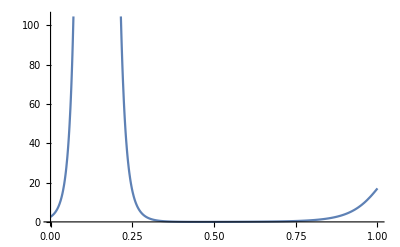

```mathematica
Plot[(Norm[Cross[dr[t],d2r[t]]])^2/(Norm[dr[t]])^5,{t,0,1}]
```

```mathematica
NIntegrate[(Norm[Cross[dr[t],d2r[t]]])^2/(Norm[dr[t]])^5,{t,0,1},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function ((Abs[2.167821-39.33155 t+204.627 t^2-«41» «1»-«1»+528.52 t^5-247.07 t^6+0. t^7]^2+Abs[-2.167821+«9»]^2+Abs[-2.281572+2.4077 t+«10»+(8 t^3)/(√Plus[«2»])+«4»]^2)/((Abs[«7»+0. Power[«2»]]^2+Abs[-2.167821 Power[«2»] t+«1»+«1»+«39» «1»]^2+Abs[«5»+1. Power[«2»]]^2)^(5/2))) is less than WorkingPrecision (50.).

322.29810752829548284255936516777530643768327636374

```mathematica
NIntegrate[N[(Norm[Cross[dr[t],d2r[t]]])^2]/N[(Norm[dr[t]])^5],{t,0,1},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function ((Abs[2.16782-39.3315 t+204.627 t^2-305.481 t^3-137.575 t^4+528.524 t^5-247.068 t^6]^2+Abs[-2.28157+«7»+150.044 t^6]^2+Abs[-2.16782+39.3315 t-220.872 t^2+336.454 t^3+161.63 t^4-565.53 t^5+256.726 t^6]^2)/((Abs[0.+1. Power[«2»]-«19» Power[«2»] t+33.627 Power[«2»] Power[«2»]+5.57137 Plus[«2»] Power[«2»]]^2+Abs[«1»]^2+Abs[-2.16782 Power[«2»] t+«1»+«1»+1. Power[«2»]]^2)^(5/2))) is less than WorkingPrecision (50.).

322.29810752829514366523308325599341191036151610228

```mathematica
curvaturesRatio[t_]=Simplify[(Norm[Cross[dr[t],d2r[t]]])^3/((Norm[dr[t]])^3*Det[{dr[t],d2r[t],d3r[t]}])]
```

1/((-32.4905+92.921 t+166.5 t^2-458. t^3-440. t^4+640. t^5+580. t^6+0``-0.5158647730980382 t^7+0``-0.5158647730980382 t^8+0``-0.5158647730980382 t^9) ((Abs[t (-2.16782+19.6658 t-23.4351 t^2+6.93718 t^3)]^2+Abs[1.-13.7078 t+62.3914 t^2-84.13 t^3+35.4465 t^4]^2+Abs[1.-15.9894 t+75.59525 t^2-101.6509 t^3+41.04508 t^4]^2)/(Abs[2.167821-39.33155 t+204.627 t^2-305.481 t^3-137.58 t^4+528.52 t^5-247.07 t^6+0. t^7]^2+Abs[2.281572-26.4077 t+91.2087 t^2-118.84 t^3-30.08 t^4+237.5 t^5-150. t^6+0. t^7]^2+Abs[2.167821-39.33155 t+220.872 t^2-336.454 t^3-161.63 t^4+565.53 t^5-256.73 t^6+0. t^7]^2))^(3/2))

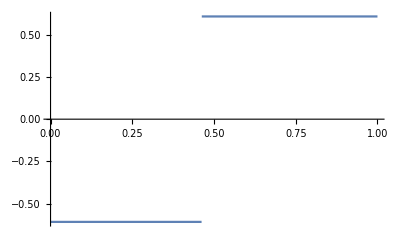

```mathematica
Plot[curvaturesRatio[t],{t,0,1}]
```

```mathematica
curvaturesRatio[0.5]
```

0.607333

```mathematica
curvaturesRatio[0.2]
```

-0.607333

Druga rešitev:

```mathematica
ξ=ξk0k2ϕ⟦2⟧⟦1⟧;
k0=ξk0k2ϕ⟦2⟧⟦2⟧;
k2=ξk0k2ϕ⟦2⟧⟦3⟧;
ϕ=ξk0k2ϕ⟦2⟧⟦4⟧;
ϕ0=0;
ϕ2=ϕ;
c0=k0-3/4;
c2=k2-3/4;
A0=√(1/2(1+λi)*ndi)Quaternion[-Sin[ϕ0],Cos[ϕ0],(μi*Cos[ϕ0]+νi*Sin[ϕ0])/(1+λi),(νi*Cos[ϕ0]-μi*Sin[ϕ0])/(1+λi)];
A2=√(1/2(1+λf)*ndf)Quaternion[-Sin[ϕ2],Cos[ϕ2],(μf*Cos[ϕ2]+νf*Sin[ϕ2])/(1+λf),(νf*Cos[ϕ2]-μf*Sin[ϕ2])/(1+λf)];
A1=c0*A0+c2*A2;
quaternionCoeffs={A0,A1,A2};
a0=A0⟦1⟧;
aV0={A0⟦2⟧,A0⟦3⟧,A0⟦4⟧};
a2=A2⟦1⟧;
aV2={A2⟦2⟧,A2⟦3⟧,A2⟦4⟧};
aV=Normalize[a0*aV2-a2*aV0+aV0×aV2];
cosψ=(a0*aV2⟦1⟧-a2*aV0⟦1⟧-aV0⟦2⟧*aV2⟦3⟧+aV0⟦3⟧*aV2⟦2⟧)/Norm[a0*aV2-a2*aV0+aV0×aV2];
ψ=ArcCos[cosψ]/Degree//FullSimplify;
aV
{cosψ,N[ψ]}
```

{-0.309913104,-0.309913104,-0.89883688}

{-0.85471531,148.728}

```mathematica
p0=pi;
p1=p0+1/5 AiA[0,0];
p2=p1+1/10(AiA[0,1]+AiA[1,0]);
p3=p2+1/30(AiA[0,2]+4AiA[1,1]+AiA[2,0]);
p4=p3+1/10(AiA[1,2]+AiA[2,1]);
p5=p4+1/5 AiA[2,2];
points = {p0,p1,p2,p3,p4,p5}
N[points]
```

{{0,0,0},{(1+√2)/(5 √(3+2 √2)),0,1/5},{0.66964733,0.2785684,0.3764617},{1.108391,1.39947,1.2853914},{1.,0.8,0.8},{1.,1.,1.}}

{{0.,0.,0.},{0.2,0.,0.2},{0.669647,0.278568,0.376462},{1.10839,1.39947,1.28539},{1.,0.8,0.8},{1.,1.,1.}}

```mathematica
Graphics3D[{Thick,BezierCurve[points, SplineDegree->5],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

-Graphics3D-

```mathematica
r[t_]=∑_(i=0)^5 points⟦i+1⟧Binomial[5,i](1-t)^(5-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[r[t]]
ExpandAll[r[t]]//TeXForm
```

{√(2/(3+2 √2)) t+t/(√(3+2 √2))+6.6964733 t^2-4 √(2/(3+2 √2)) t^2-(4 t^2)/(√(3+2 √2))-3.00551 t^3-1.0784 t^4+1.38744 t^5,2.785684 t^2+5.637648 t^3-15.63235 t^4+8.209016 t^5,t-0.235383 t^2+7.560063 t^3-14.41398 t^4+7.089297 t^5}

\left\{1.387437 t^5-1.078401 t^4-3.005510 t^3-\frac{4 t^2}{\sqrt{3+2 \sqrt{2}}}-4 \sqrt{\frac{2}{3+2 \sqrt{2}}} t^2+6.6964733 t^2+\frac{t}{\sqrt{3+2 \sqrt{2}}}+\sqrt{\frac{2}{3+2 \sqrt{2}}} t,8.209016 t^5-15.632347 t^4+5.637648 t^3+2.7856840 t^2,7.089297 t^5-14.413976 t^4+7.560063
   t^3-0.2353830 t^2+t\right\}

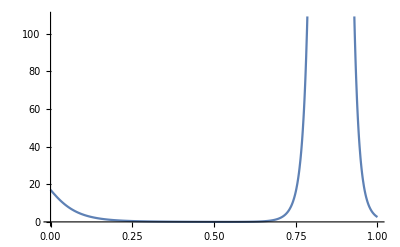

```mathematica
Plot[(Norm[Cross[dr[t],d2r[t]]])^2/(Norm[dr[t]])^5,{t,0,1}]
```

```mathematica
NIntegrate[(Norm[Cross[dr[t],d2r[t]]])^2/(Norm[dr[t]])^5,{t,0,1},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function ((Abs[5.863713-87.39343 t+24 √Times[«2»] t+(24 t)/(√Plus[«2»])+65.9585 t^2-«1»-(24 «1»)/(√(«1»))+503.895 t^3+8 √Times[«2»] t^3+(8 t^3)/(√Plus[«2»])+«4»]^2+Abs[5.571368+«9»+0. «1»]^2+Abs[-5.571368-33.82589 t+«7»+0. t^7]^2)/((Abs[Plus[«2»] Power[«2»] Power[«2»]+«6»+0. Power[«2»]]^2+Abs[«1»]^2+Abs[Plus[«2»]^4+«4»+1. Power[«2»]]^2)^(5/2))) is less than WorkingPrecision (50.).

322.29810752829548313435921389071156250353451273678

```mathematica
NIntegrate[N[(Norm[Cross[dr[t],d2r[t]]])^2]/N[(Norm[dr[t]])^5],{t,0,1},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function ((Abs[5.86371-63.3934 t+41.9585 t^2+511.895 t^3-1200.97 t^4+953.882 t^5-247.068 t^6]^2+Abs[-5.57137-33.8259 t+«6»+150.044 t^6]^2+Abs[5.57137+33.8259 t-46.1432 t^2-462.19 t^3+1184.87 t^4-974.825 t^5+256.726 t^6]^2)/((Abs[0.+1. Power[«2»]+«18» Power[«1»] t+13.1623 Power[«2»] Power[«2»]-2.16782 Plus[«2»] Power[«2»]]^2+Abs[5.57137 Power[«2»] t+«1»-«1»+1. Power[«2»]]^2+Abs[«1»]^2)^(5/2))) is less than WorkingPrecision (50.).

322.29810752823985952068071475345955981396631347144

```mathematica
curvaturesRatio[t_]=Simplify[(Norm[Cross[dr[t],d2r[t]]])^3/((Norm[dr[t]])^3*Det[{dr[t],d2r[t],d3r[t]}])]
```

1/((551.5334-3983.06 t+11273. t^2-15805. t^3+11480. t^4-4130. t^5+580. t^6+0``-0.346507657785552 t^7+0``-0.346507657785552 t^8+0``-0.346507657785552 t^9) ((Abs[t (5.57137+16.9129 t-62.5294 t^2+41.0451 t^3)]^2+Abs[1.+5.3929 t-9.01653 t^2-4.3136 t^3+6.93718 t^4]^2+Abs[1.-0.470766 t+22.6802 t^2-57.6559 t^3+35.4465 t^4]^2)/(Abs[5.863713-63.39343 t+41.9585 t^2+511.895 t^3-1200.97 t^4+953.88 t^5-247.07 t^6+0. t^7]^2+Abs[5.571368+33.82589 t-46.1432 t^2-462.19 t^3+1184.87 t^4-974.82 t^5+256.73 t^6+0. t^7]^2+Abs[5.571368+33.82589 t-321.9099 t^2+865.498 t^3-1093.47 t^4+662.81 t^5-150. t^6+0. t^7]^2))^(3/2))

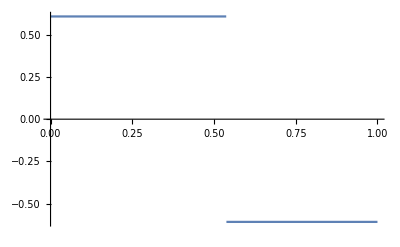

```mathematica
Plot[curvaturesRatio[t],{t,0,1}]
```

```mathematica
curvaturesRatio[0.2]
```

0.607333

```mathematica
curvaturesRatio[0.6]
```

-0.607333

Tretja rešitev:

```mathematica
ξ=ξk0k2ϕ⟦3⟧⟦1⟧;
k0=ξk0k2ϕ⟦3⟧⟦2⟧;
k2=ξk0k2ϕ⟦3⟧⟦3⟧;
ϕ=ξk0k2ϕ⟦3⟧⟦4⟧;
ϕ0=0;
ϕ2=ϕ;
c0=k0-3/4;
c2=k2-3/4;
A0=√(1/2(1+λi)*ndi)Quaternion[-Sin[ϕ0],Cos[ϕ0],(μi*Cos[ϕ0]+νi*Sin[ϕ0])/(1+λi),(νi*Cos[ϕ0]-μi*Sin[ϕ0])/(1+λi)];
A2=√(1/2(1+λf)*ndf)Quaternion[-Sin[ϕ2],Cos[ϕ2],(μf*Cos[ϕ2]+νf*Sin[ϕ2])/(1+λf),(νf*Cos[ϕ2]-μf*Sin[ϕ2])/(1+λf)];
A1=c0*A0+c2*A2;
quaternionCoeffs={A0,A1,A2};
a0=A0⟦1⟧;
aV0={A0⟦2⟧,A0⟦3⟧,A0⟦4⟧};
a2=A2⟦1⟧;
aV2={A2⟦2⟧,A2⟦3⟧,A2⟦4⟧};
aV=Normalize[a0*aV2-a2*aV0+aV0×aV2];
cosψ=(a0*aV2⟦1⟧-a2*aV0⟦1⟧-aV0⟦2⟧*aV2⟦3⟧+aV0⟦3⟧*aV2⟦2⟧)/Norm[a0*aV2-a2*aV0+aV0×aV2];
ψ=ArcCos[cosψ]/Degree//FullSimplify;
aV
{cosψ,N[ψ]}
```

{0.354663971,0.354663971,0.865116718}

{0.862515197,30.3998}

```mathematica
p0=pi;
p1=p0+1/5 AiA[0,0];
p2=p1+1/10(AiA[0,1]+AiA[1,0]);
p3=p2+1/30(AiA[0,2]+4AiA[1,1]+AiA[2,0]);
p4=p3+1/10(AiA[1,2]+AiA[2,1]);
p5=p4+1/5 AiA[2,2];
points = {p0,p1,p2,p3,p4,p5}
N[points]
```

{{0,0,0},{(1+√2)/(5 √(3+2 √2)),0,1/5},{0.531075526,0.1109995,0.37683001},{0.8890005,0.46892447,0.62316999},{1.,0.8,0.8},{1.,1.,1.}}

{{0.,0.,0.},{0.2,0.,0.2},{0.531076,0.111,0.37683},{0.889,0.468924,0.62317},{1.,0.8,0.8},{1.,1.,1.}}

```mathematica
Graphics3D[{Thick,BezierCurve[points, SplineDegree->5],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

-Graphics3D-

```mathematica
r[t_]=∑_(i=0)^5 points⟦i+1⟧Binomial[5,i](1-t)^(5-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[r[t]]
ExpandAll[r[t]]//TeXForm
```

{√(2/(3+2 √2)) t+t/(√(3+2 √2))+5.31075526 t^2-4 √(2/(3+2 √2)) t^2-(4 t^2)/(√(3+2 √2))-1.042261 t^3-0.8477442 t^4+0.5792497 t^5,1.109995 t^2+1.35926 t^3-2.048504 t^4+0.5792497 t^5,t-0.2316999 t^2+0.9267996 t^3-1.158499 t^4+0.4633998 t^5}

\left\{0.5792497 t^5-0.8477442 t^4-1.0422608 t^3-\frac{4 t^2}{\sqrt{3+2 \sqrt{2}}}-4 \sqrt{\frac{2}{3+2 \sqrt{2}}} t^2+5.31075526 t^2+\frac{t}{\sqrt{3+2 \sqrt{2}}}+\sqrt{\frac{2}{3+2 \sqrt{2}}} t,0.5792497 t^5-2.0485045 t^4+1.3592597 t^3+1.10999500 t^2,0.4633998 t^5-1.1584995
   t^4+0.9267996 t^3-0.23169990 t^2+t\right\}

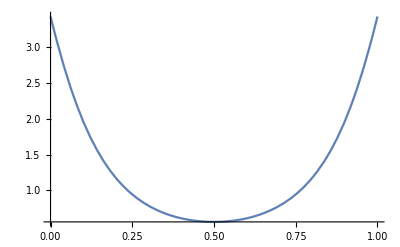

```mathematica
Plot[(Norm[Cross[dr[t],d2r[t]]])^2/(Norm[dr[t]])^5,{t,0,1}]
```

```mathematica
NIntegrate[(Norm[Cross[dr[t],d2r[t]]])^2/(Norm[dr[t]])^5,{t,0,1},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function ((Abs[-2.21999-8.155558 t+32.64415 t^2-«40» t^3+«1»+2.791 t^5-5.5643 t^6+0. t^7]^2+Abs[«13»+«4»]^2+Abs[2.21999+«9»+0. t^7]^2)/((Abs[Plus[«2»] Power[«2»] Power[«2»]+«5»+0. Power[«2»]]^2+Abs[«1»]^2+Abs[Plus[«2»]^4+«3»+1. Power[«2»]]^2)^(5/2))) is less than WorkingPrecision (50.).

1.2735954414932029834324168438581174196631147886199

```mathematica
NIntegrate[N[(Norm[Cross[dr[t],d2r[t]]])^2]/N[(Norm[dr[t]])^5],{t,0,1},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function ((Abs[-2.21999-8.15556 t+32.6442 t^2-39.7541 t^3+23.3437 t^4+2.79097 t^5-5.56432 t^6]^2+Abs[«8»+30.595 t^5-5.56432 t^6]^2+Abs[2.21999+8.15556 t-6.95069 t^2-16.3205 t^3+42.9373 t^4-41.7324 t^5+13.9108 t^6]^2)/((Abs[0.+1. Power[«2»]+«18» Power[«1»] t+10.7377 Power[«2»] Power[«2»]+2.21999 Plus[«2»] Power[«2»]]^2+Abs[«1»]^2+Abs[2.21999 Power[«2»] t+«1»+«1»+1. Power[«2»]]^2)^(5/2))) is less than WorkingPrecision (50.).

1.2735954414932020373508220189157265599743251814245

```mathematica
curvaturesRatio[t_]=Simplify[(Norm[Cross[dr[t],d2r[t]]])^3/((Norm[dr[t]])^3*Det[{dr[t],d2r[t],d3r[t]}])]
```

1/((51.-170. t+350. t^2-430. t^3+380. t^4-200. t^5+67. t^6+0. t^7+0. t^8+0. t^9) ((Abs[t (2.21999+4.077779 t-8.194018 t^2+2.896249 t^3)]^2+Abs[1.-0.4633998 t+2.780399 t^2-4.633998 t^3+2.316999 t^4]^2+Abs[1.+2.62151 t-3.12678 t^2-3.39098 t^3+2.89625 t^4]^2)/(Abs[3.0849103-11.81436 t-2.1108 t^2+29.7559 t^3-46.166 t^4+30.595 t^5-5.5643 t^6+0. t^7]^2+Abs[2.21999+8.155558 t-32.64415 t^2+39.7541 t^3-23.3437 t^4-2.791 t^5+5.5643 t^6+0. t^7]^2+Abs[2.21999+8.155558 t-6.95069 t^2-16.321 t^3+42.937 t^4-41.732 t^5+13.911 t^6+0. t^7]^2))^(3/2))

```mathematica
Plot[curvaturesRatio[t],{t,0,1}]
```

-Graphics-

```mathematica
curvaturesRatio[0.5]
```

0.586692

Četrta rešitev:

```mathematica
ξ=ξk0k2ϕ⟦4⟧⟦1⟧;
k0=ξk0k2ϕ⟦4⟧⟦2⟧;
k2=ξk0k2ϕ⟦4⟧⟦3⟧;
ϕ=ξk0k2ϕ⟦4⟧⟦4⟧;
ϕ0=0;
ϕ2=ϕ;
c0=k0-3/4;
c2=k2-3/4;
A0=√(1/2(1+λi)*ndi)Quaternion[-Sin[ϕ0],Cos[ϕ0],(μi*Cos[ϕ0]+νi*Sin[ϕ0])/(1+λi),(νi*Cos[ϕ0]-μi*Sin[ϕ0])/(1+λi)];
A2=√(1/2(1+λf)*ndf)Quaternion[-Sin[ϕ2],Cos[ϕ2],(μf*Cos[ϕ2]+νf*Sin[ϕ2])/(1+λf),(νf*Cos[ϕ2]-μf*Sin[ϕ2])/(1+λf)];
A1=c0*A0+c2*A2;
quaternionCoeffs={A0,A1,A2};
a0=A0⟦1⟧;
aV0={A0⟦2⟧,A0⟦3⟧,A0⟦4⟧};
a2=A2⟦1⟧;
aV2={A2⟦2⟧,A2⟦3⟧,A2⟦4⟧};
aV=Normalize[a0*aV2-a2*aV0+aV0×aV2];
cosψ=(a0*aV2⟦1⟧-a2*aV0⟦1⟧-aV0⟦2⟧*aV2⟦3⟧+aV0⟦3⟧*aV2⟦2⟧)/Norm[a0*aV2-a2*aV0+aV0×aV2];
ψ=ArcCos[cosψ]/Degree//FullSimplify;
aV
{cosψ,N[ψ]}
```

{0.354663971,0.354663971,0.865116718}

{0.862515197,30.3998}

```mathematica
p0=pi;
p1=p0+1/5 AiA[0,0];
p2=p1+1/10(AiA[0,1]+AiA[1,0]);
p3=p2+1/30(AiA[0,2]+4AiA[1,1]+AiA[2,0]);
p4=p3+1/10(AiA[1,2]+AiA[2,1]);
p5=p4+1/5 AiA[2,2];
points = {p0,p1,p2,p3,p4,p5}
N[points]
```

{{0,0,0},{(1+√2)/(5 √(3+2 √2)),0,1/5},{-0.582386192,-0.26231017,-0.21787854},{1.2623102,1.5823862,1.2178785},{1.,0.8,0.8},{1.,1.,1.}}

{{0.,0.,0.},{0.2,0.,0.2},{-0.582386,-0.26231,-0.217879},{1.26231,1.58239,1.21788},{1.,0.8,0.8},{1.,1.,1.}}

```mathematica
Graphics3D[{Thick,BezierCurve[points, SplineDegree->5],Green,Line[points],Red,PointSize[Large],Point[points]},Axes-> True,AxesLabel-> {"x","y","z"},LabelStyle->Directive[Large],BoxRatios->{1, 1, 1},Boxed->False]
```

-Graphics3D-

```mathematica
r[t_]=∑_(i=0)^5 points⟦i+1⟧Binomial[5,i](1-t)^(5-i)t^i;
dr[t_]=D[r[t],t];
d2r[t_]=D[dr[t],t];
d3r[t_]=D[d2r[t],t];
ExpandAll[r[t]]
ExpandAll[r[t]]//TeXForm
```

{√(2/(3+2 √2)) t+t/(√(3+2 √2))-5.82386192 t^2-4 √(2/(3+2 √2)) t^2-(4 t^2)/(√(3+2 √2))+36.094687 t^3-41.717789 t^4+15.446964 t^5,-2.6231017 t^2+23.693167 t^3-35.517029 t^4+15.446964 t^5,t-6.17878543 t^2+24.715142 t^3-30.893927 t^4+12.357571 t^5}

\left\{15.4469636 t^5-41.7177891 t^4+36.0946874 t^3-\frac{4 t^2}{\sqrt{3+2 \sqrt{2}}}-4 \sqrt{\frac{2}{3+2 \sqrt{2}}} t^2-5.82386192 t^2+\frac{t}{\sqrt{3+2 \sqrt{2}}}+\sqrt{\frac{2}{3+2 \sqrt{2}}} t,15.4469636 t^5-35.5170288 t^4+23.6931669 t^3-2.62310166 t^2,12.3575709
   t^5-30.8939272 t^4+24.7151417 t^3-6.17878543 t^2+t\right\}

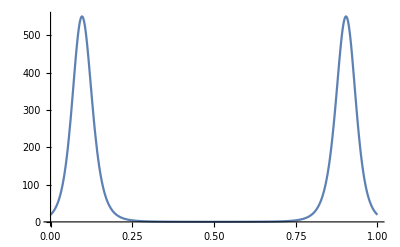

```mathematica
Plot[(Norm[Cross[dr[t],d2r[t]]])^2/(Norm[dr[t]])^5,{t,0,1}]
```

```mathematica
NIntegrate[(Norm[Cross[dr[t],d2r[t]]])^2/(Norm[dr[t]])^5,{t,0,1},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function ((Abs[5.2462033-142.159 t+915.5923 t^2-«1»+«1»-2669.52 t^5+766.26 t^6+0. t^7]^2+Abs[-7.290153+«12»+«4»]^2+Abs[-5.2462033+«9»+0. t^7]^2)/((Abs[«8»+0. Power[«2»]]^2+Abs[«1»]^2+Abs[«6»+1. Power[«2»]]^2)^(5/2))) is less than WorkingPrecision (50.).

89.576304830912843899736860686763832111889741749062

```mathematica
NIntegrate[N[(Norm[Cross[dr[t],d2r[t]]])^2]/N[(Norm[dr[t]])^5],{t,0,1},WorkingPrecision->50]
```

NIntegrate::precw: The precision of the argument function ((Abs[-5.2462+142.159 t-1254.67 t^2+4140.69 t^3-6859.49 t^4+5746.98 t^5-1915.66 t^6]^2+Abs[5.2462-142.159 t+«6»+766.263 t^6]^2+Abs[-7.29015+68.2773 t-11.2255 t^2-669.931 t^3+1787.21 t^4-1928.06 t^5+766.263 t^6]^2)/((Abs[0.+1. Power[«2»]-«19» Power[«2»] t+55.3409 Power[«2»] Power[«2»]-5.2462 Plus[«2»] Power[«2»]]^2+Abs[«1»]^2+Abs[«6»+1. Power[«2»]]^2)^(5/2))) is less than WorkingPrecision (50.).

89.576304830912142440267236609873678981608958451405

```mathematica
curvaturesRatio[t_]=Simplify[(Norm[Cross[dr[t],d2r[t]]])^3/((Norm[dr[t]])^3*Det[{dr[t],d2r[t],d3r[t]}])]
```

1/((-678.1644+4851.369 t-16419.7 t^2+32332. t^3-39150. t^4+27590. t^5-9200. t^6+0``-0.6991302289996026 t^7+0``-0.6991302289996026 t^8+0``-0.6991302289996026 t^9) ((Abs[t (-5.246203+71.0795 t-142.0681 t^2+77.23482 t^3)]^2+Abs[1.-12.35757 t+74.14543 t^2-123.5757 t^3+61.78785 t^4]^2+Abs[1.-19.647724 t+108.28406 t^2-166.87116 t^3+77.234818 t^4]^2)/(Abs[7.290153-68.27727 t+11.225 t^2+669.931 t^3-1787.21 t^4+1928.06 t^5-766.26 t^6+0. t^7]^2+Abs[5.2462033-142.159 t+915.5923 t^2-2523.566 t^3+3640.85 t^4-2669.52 t^5+766.26 t^6+0. t^7]^2+Abs[5.2462033-142.159 t+1254.675 t^2-4140.689 t^3+6859.491 t^4-5746.98 t^5+1915.66 t^6+0. t^7]^2))^(3/2))

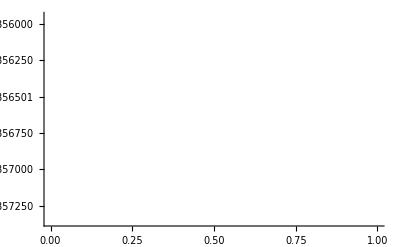

```mathematica
Plot[curvaturesRatio[t],{t,0,1}]
```

```mathematica
curvaturesRatio[0.5]
```

-0.586692